## Code

#### Text

```mathematica
figTextStyles=
{
FontFamily->"CMU Sans Serif",
FontSize->24,
SingleLetterItalics->False,
ShowStringCharacters->False
};
figTextCustomizations=
<|
"Small"->{FontSize->20},
"Title"->{FontWeight->Bold, FontSize->45, FontFamily->"CMU Serif"},
"PlotMarker2"->{FontSize->18},
"PlotMarkerTriangle"->{FontSize->18}
|>;
```

```mathematica
figStyleText//Clear
```

```mathematica
figStyleText[text_, cust_:None]:=
With[
{
opts=
Normal@
Merge[
{
figTextStyles,
Lookup[figTextCustomizations, cust, {}]
},
Last
]},
Style[text, 
Sequence@@
Join[
opts,
{
SubscriptBoxOptions->opts,
SuperscriptBoxOptions->opts,
SubsuperscriptBoxOptions->opts
}
]
]
];
figStyleTextBoxWrap[b_, cust_:None]:=
ToBoxes[figStyleText[T, cust]]/."T"->b
figStyleTextBoxes[b_, cust_:None]:=
figStyleTextBoxWrap@ToBoxes[b];
```

#### General

##### Reusable Bits

```mathematica
colorScheme=
{Hue[0.49, 1, 0.84],RGBColor[0., 0.596078, 0.109804],RGBColor[0.6, 0.4, 0.2],RGBColor[0.5, 0, 0.5],Hue[0.14, 1, 1],RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843]};
colorSchemeO=
{GrayLevel[0],RGBColor[0., 0.596078, 0.109804], RGBColor[0.192157, 0.388235, 0.807843],RGBColor[0.790588, 0.201176, 0.], Hue[0.14, 1, 1], RGBColor[0.5, 0, 0.5], Hue[0.49, 1, 0.84]};
lineStyleScheme={Thick, Dashed, DotDashed, Dotted};
customCF=
ColorDataFunction[201, 
"Indexed", 
{1, ∞, 1},
colorScheme[[Mod[#1, Length@colorScheme, 1]]]&
];
cfO=
ColorDataFunction[213, 
"Indexed", 
{1, ∞, 1},
colorSchemeO[[Mod[#1, Length@colorSchemeO, 1]]]&
];
```

```mathematica
plotMarkerEqBasic=
figStyleText["•"];
plotMarkerAveBasic=
Overlay[{Style[figStyleText["•"], White], figStyleText["◦"]},
ContentPadding->False,
BaselinePosition->Bottom
];
```

```mathematica
$plotMarkers=
<|
"Default"->
<|
"Eq"->plotMarkerEqBasic,
"Av"->plotMarkerAveBasic
|>,
"Diamond"->
<|
"Eq"->
figStyleText["◆", "PlotMarker2"],
"Av"->
Overlay[{
figStyleText[Style["◆", White], "PlotMarker2"], figStyleText[Style["◇", FontSize->Lookup[figTextCustomizations["PlotMarker2"], FontSize]+3], "PlotMarker2"
]},
ContentPadding->False,
BaselinePosition->Bottom
]
|>,
"Triangle"->
<|
"Eq"->
figStyleText["▼", "PlotMarkerTriangle"],
"Av"->
Overlay[{
figStyleText[Style["▼", White], "PlotMarkerTriangle"], figStyleText["▽", "PlotMarkerTriangle"
]},
ContentPadding->False,
BaselinePosition->Bottom
]
|>
|>;
```

```mathematica
labelΔRe="ΔR_e";
labelΔR0="ΔR_0";
labelΔωH="Δω";
labelΔωA="Δν";
labelΔR="`` and ``"~TemplateApply~{labelΔRe, labelΔR0};
labelΔω="`` and ``"~TemplateApply~{labelΔωH, labelΔωA};
labelSlopeH="``/``"~TemplateApply~{labelΔωH, labelΔRe};
labelSlopeA="``/``"~TemplateApply~{labelΔωA,labelΔR0};
labelSlope="`` and ``"~TemplateApply~{labelSlopeH, labelSlopeA};
labelΔRUnits="0.001Å";
labelΔωUnits="cm^-1";
labelSlopeUnits=labelΔωUnits<>"/"<>labelΔRUnits;
labelΔRFull=TemplateApply["`` (``)", {labelΔR, labelΔRUnits}];
labelΔωFull=TemplateApply["`` (``)", {labelΔω, labelΔωUnits}];
labelSlopeFull=TemplateApply["`` (``)", {labelSlope, labelSlopeUnits}];
labelSlopeHFull=TemplateApply["`` (``)", {labelSlopeH, labelSlopeUnits}];
labelSlopeAFull=TemplateApply["`` (``)", {labelSlopeA, labelSlopeUnits}];
```

##### Styles

```mathematica
figPlotStyles=
{
Axes->False,
Frame->True,(*
FrameTicks->{{Automatic, None}, {Automatic, None}},*)
FrameStyle->{
{Directive[AbsoluteThickness->1,Sequence@@figTextStyles ,Black], Opacity[0]}, {Directive[AbsoluteThickness->1, Sequence@@figTextStyles , Black], Opacity[0]}
},
PlotStyle->(Directive[AbsolutePointSize@5, customCF[#]]&),
PlotRange->All,
PlotMarkers->plotMarkerEqBasic,
ImageSize->700,
AspectRatio->1
};
```

##### plotStyle*

```mathematica
plotStyleNumber[fname_]:=
Catch[
MapIndexed[
If[StringContainsQ[fname, #], Throw[{#2[[1]]}], #2[[1]]+1]&,
{
"F","Cl","Br","I",
"X", "H3O", "H2O"
}
]
][[-1]];
plotStyleFromNumber[n_]:=
Lookup[figPlotStyles, PlotStyle][n];
plotStyleFromName[t_]:=
plotStyleFromNumber@plotStyleNumber[t]
```

##### Boxes

```mathematica
h30Box=
RowBox[{
SubscriptBox["H", 3],
AdjustmentBox[SuperscriptBox["O", "+"], BoxMargins->{{-.15, 0}, {0, 0}}]}
];
```

```mathematica
h20Box=
RowBox[{
SubscriptBox["H", 2],
AdjustmentBox["O", BoxMargins->{{-.15, 0}, {0, 0}}]}
];
```

##### $keyMap

```mathematica
(*$keyMap=
AssociationMap[
"X=`` ``"~TemplateApply~
MapAt[
Replace[{"equ"->"eq.", "ave"->"vib. ave."}],
StringSplit[#, "_"][[{1, -1}]],
-1
]&,
Keys@KeySelect[dats, Not@*StringStartsQ["OH"]]
]~Join~
AssociationMap[
"OH...O in `` ``"~TemplateApply~
MapAt[
Replace[
{
"X"->"X^-(H_2O)_n",
"H3O+"->"H_3O^+(H_2O)_n",
"H2O"->"(H_2O)_n"
}],
MapAt[
Replace[{"equ"->"eq.", "ave"->"vib. ave."}],
StringSplit[#, "_"][[{3, -1}]],
-1
],
1
]&,
Keys@KeySelect[dats, StringStartsQ["OH"]]
];*)
```

```mathematica
$keyMap=
Join[
AssociationThread[
Map[#[[1]]<>"_shifts_"<>#[[2]]&, 
Tuples[{{"F", "Cl", "Br", "I"}, {"equ", "avg"}}]
],
Map[
Row[Flatten@{Row[{"OH...", Superscript[#[[1]], "-"]}], #[[2]]}, " "]&,
Tuples[{{"F", "Cl", "Br", "I"}, {"eq.", {"vib.", "avg."}}}]
]
],
AssociationThread[
Map[TemplateApply["OH_in_``_shifts_``", #]&, 
Tuples[{{"X", "H3O+", "H2O"}, {"equ", "avg"}}]
],
Map[
Row[
{"OH...O","in", 
Row[
Flatten@{
#[[1]],
RawBoxes@
AdjustmentBox[
SubscriptBox[
RowBox[
{
"\"(\"", 
AdjustmentBox[h20Box, BoxMargins->{{-0.25,0},{0,0}}] ,
"\")\""
}
],
"\"n\""
],
BoxMargins->{{0,0},{0,0}}
],
#[[2]]
}
] 
},
" "
]&,
Tuples[{{Superscript["X", "-"], RawBoxes@h30Box, ""}, {"eq.", {"vib.", "avg."}}}]
]
]
];
```

```mathematica
colFunc=FirstCase[Lookup[figPlotStyles, PlotStyle], _ColorDataFunction|_ColorFunction|_ColorData, customCF, ∞, Heads->True];
```

#### Plotting Functions

##### Hacks

##### Styles

```mathematica
cleanListPlotStyles[data_][ops_]:=
With[
{
ps=Lookup[ops, PlotStyle],
dlen=If[Depth[data]>3, Length@data, 1]
},
Join[
{
PlotStyle->ps/@Range[dlen]
},
ops
]
];
cleanPlotStyles[fns_][ops_]:=
With[
{
ps=Lookup[ops, PlotStyle],
dlen=If[ListQ@Unevaluated[fns], Length@Thread[Hold[fns]], 1]
},
Join[
{
PlotStyle->ps/@Range[dlen]
},
ops
]
];
```

##### Plots

```mathematica
figListPlot[data_, {ax1_, ax2_}, ops___]:=
ListPlot[data,
FilterRules[
cleanListPlotStyles[data]@
Normal@Merge[
Flatten@{
{ops,  FrameLabel->{{ax2, None}, {ax1, None}}},
figPlotStyles
},
First
], 
Options@ListPlot
]
]/."Arial"->Lookup[figPlotStyles, FontFamily];
figListLinePlot[data_, {ax1_, ax2_}, ops___]:=
ListLinePlot[data,
FilterRules[
cleanListPlotStyles[data]@
Normal@Merge[
Flatten@{
{ops,  FrameLabel->{{ax2, None}, {ax1, None}}},
figPlotStyles
},
First
], 
Options@ListLinePlot
]
]/."Arial"->Lookup[figPlotStyles, FontFamily];
figPlot[fn_, spec_, {ax1_, ax2_}, ops___]:=
Plot[fn,
spec,
Evaluate@
FilterRules[
cleanPlotStyles[fn]@
Normal@Merge[
Flatten@{
{ops,  FrameLabel->{{figStyleText@ax2, None}, {figStyleText@ax1, None}}},
figPlotStyles
},
First
], 
Options@Plot
]
]/."Arial"->Lookup[figPlotStyles, FontFamily];
figPlot~SetAttributes~HoldAll
figListContourPlot[data_, {ax1_, ax2_}, ops___]:=
Replace[h:Except[_Graphics]:>ReplacePart[h, 2->(h[[2]]/."Arial"->Lookup[figPlotStyles, FontFamily])]]@
ListContourPlot[
data,
Evaluate@
FilterRules[
cleanPlotStyles[{1}]@
Normal@Merge[
Flatten@{
{ops,  FrameLabel->{{figStyleText@ax2, None}, {figStyleText@ax1, None}}},
figPlotStyles
},
First
], 
Options@ListContourPlot
]
];
figListDensityPlot[data_, {ax1_, ax2_}, ops___]:=
Replace[h:Except[_Graphics]:>ReplacePart[h, 2->(h[[2]]/."Arial"->Lookup[figPlotStyles, FontFamily])]]@ListDensityPlot[
data,
Evaluate@
FilterRules[
cleanPlotStyles[{1}]@
Normal@Merge[
Flatten@{
{ops,  FrameLabel->{{figStyleText@ax2, None}, {figStyleText@ax1, None}}},
figPlotStyles
},
First
], 
Options@ListDensityPlot
]
];
figContourPlot[fn_, spec1_, spec2_, {ax1_, ax2_}, ops___]:=
ContourPlot[
fn,
spec1,
spec2,
Evaluate@
FilterRules[
cleanPlotStyles[fn]@
Normal@Merge[
Flatten@{
{ops,  FrameLabel->{{figStyleText@ax2, None}, {figStyleText@ax1, None}}},
figPlotStyles
},
First
], 
Options@ContourPlot
]
];
figContourPlot~SetAttributes~HoldAll;
figSpecialContourPlot[fn_, spec1_, spec2_, {ax1_, ax2_}, ops___]:=
contourRegionPlot[
fn,
spec1,
spec2,
Evaluate@
FilterRules[
cleanPlotStyles[fn]@
Normal@Merge[
Flatten@{
{ops,  FrameLabel->{{figStyleText@ax2, None}, {figStyleText@ax1, None}}},
figPlotStyles
},
First
], 
Options@ContourPlot
]
];
figSpecialContourPlot~SetAttributes~HoldAll;
figDensityPlot[fn_, spec1_, spec2_, {ax1_, ax2_}, ops___]:=
DensityPlot[
fn,
spec1,
spec2,
Evaluate@
FilterRules[
cleanPlotStyles[fn]@
Normal@Merge[
Flatten@{
{ops,  FrameLabel->{{figStyleText@ax2, None}, {figStyleText@ax1, None}}},
figPlotStyles
},
First
], 
Options@DensityPlot
]
];
figDensityPlot~SetAttributes~HoldAll
```

##### Ticks

```mathematica
ticksFromPlot//Clear
ticksFromPlot[
p_,
 n:_Integer?Positive:10,
 scale:_?(-1<#<1&):.1, 
dropMins:{True|False,True|False}:{True, True},
tickScaling:_?NumericQ|Automatic:Automatic
 ]:=
Block[
{
pr=PlotRange@p,
ar=If[tickScaling==Automatic, AspectRatio/.Options[p, AspectRatio],tickScaling],
ph,
st,
cleanTicks
},
st=
SortBy[Abs@*First]@
Charting`ScaledTicks[
{Identity, Identity}
][
With[{m=Mean@#},
Sequence@@((1+scale)*(#-m)+m)
], 
n
]&/@pr;
ph=ar*.01;
cleanTicks=
ReplacePart[st,
{
{_, _, -1}->{AbsoluteThickness[1]},
{_, _, 3}->{ph, 0.}
}
];
cleanTicks=
MapThread[
If[#2[[1]]==0,
Prepend[#,
ReplacePart[#[[1]], 
{
1->0,
2->
If[NumericQ@#[[1, 2]],
0,
ReplacePart[#[[1, 2]], 1->If[IntegerPart[#[[1, 1]]]==#[[1, 1]], 0, 0.]
]
]
}
]
],
#
]&,
{
cleanTicks,
pr
}
];
cleanTicks=
MapThread[
If[Min[Abs[#2]]/(Abs[Subtract@@#2])<10^-5,
Prepend[#,
ReplacePart[#[[1]], 
{
1->0,
2->
If[NumericQ@#[[1, 2]],
0,
ReplacePart[#[[1, 2]], 1->If[IntegerPart[#[[1, 1]]]==#[[1, 1]], 0, 0.]
]
]
}
]
],
#
]&,
{
cleanTicks,
pr
}
];
MapThread[
If[#2&&Rescale[Min@#[[All, 1]], #3]<-.01,
ReplacePart[#, {If[#[[1, 1]]<#[[-1, 1]], 1, -1], 3}->{0., 0.}],
#
]&,
{
cleanTicks,
dropMins,
pr
}
]
]
```

##### insetLegend

```mathematica
insetLegend[plot_, where_:Scaled[{.05, .95}], anchor_:{Left, Top}]:=Show[#[[1]], Epilog->Inset[#[[2, 1]], where, anchor]]&@plot;
```

##### showTicks

```mathematica
showTicks[p_]:=
Show[#, FrameTicks->ticksFromPlot@#]&@p
```

##### dataLabelLegend

```mathematica
dataLabelLegend//Clear;
dataLabelLegend[keys_, pms_:"Default"]:=
Grid[
KeyValueMap[
{Style[
If[StringEndsQ[#, "avg"], $plotMarkers[pms, "Av"], $plotMarkers[pms, "Eq"]], 
plotStyleFromName@#
], figStyleText[#2, "Small"]}&,
$keyMap[[
2*plotStyleNumber[#]-If[StringEndsQ[#, "avg"], 0, 1]&/@SortBy[keys, {plotStyleNumber, StringEndsQ["avg"]}]
]]
],
Alignment->Left
]
```

#### File Functions

##### Figs

```mathematica
figureFile[name_]:=
With[{nameBase=StringSplit[name]},
Internal`WithLocalSettings[
SetDirectory[NotebookDirectory[]],
ExpandFileName@If[FileExtension[name]=="", name<>".pdf", name],
ResetDirectory[]
]
];
presFigFile[presentPath_]:=
figureFile["../../Presentation/figures/"<>presentPath]
```

```mathematica
figureData[name_]:=
FileNameJoin@{NotebookDirectory[], "Data", name};
```

##### Export

expFig

```mathematica
expFig//Clear
expFig[name_, fig_, fn:Except[_?OptionQ]:printBasedExport1, ops:OptionsPattern[]]:=
fn[name, fig, ops];
expFig[name_][fig_, fn:Except[_?OptionQ]:printBasedExport1, ops:OptionsPattern[]]:=
expFig[name, fig, ops];
```

```mathematica
expEcho//Clear
expEcho[name_, fig_,  fn:Except[_?OptionQ]:printBasedExport1, ops:OptionsPattern[]]:=
(expFig[name, fig, ops];fig);
expEcho[name_][fig_,  fn:Except[_?OptionQ]:printBasedExport1, ops:OptionsPattern[]]:=
expEcho[name, fig, ops]
```

baseExport

```mathematica
baseExport[name_, fig_]:=
Export[
If[FileNameDepth[name]==1,
figureFile[FileBaseName@name<>".pdf"],
name
],
fig
];
```

overrideExport1

```mathematica
overrideExport1[name_, fig_]:=
Internal`InheritedBlock[{NotebookPrint},
Unprotect[NotebookPrint];
NotebookPrint[a___]/;!TrueQ[$flag]:=
Block[{$flag=True},
NotebookPrint@@Append[DeleteCases[{a}, Interactive->_],Interactive->True]
];
DownValues[NotebookPrint]=SortBy[DownValues[NotebookPrint], {FreeQ[$flag]}];
Export[
If[FileNameDepth[name]==1,
figureFile[FileBaseName@name<>".pdf"],
name
], 
fig
]
]
```

printBasedExport1

```mathematica
getPrintNotebookExpr[expr_]:=
Switch[
Head@expr,
Notebook,
expr,
Cell,
getPrintNotebookExpr@Notebook[{expr}],
BoxData,
getPrintNotebookExpr@Cell[expr, "Output"],
TextData,
getPrintNotebookExpr[Cell[expr, "Text"]],
CellObject,
getPrintNotebookExpr[NotebookRead[expr]],
NotebookObject,
getPrintNotebookExpr[NotebookGet[expr]],
_,
getPrintNotebookExpr[BoxData@ToBoxes@expr]
];
getExprDims[expr_]:=
Rasterize[expr, "RasterSize"];
Options[printBasedExport1]=
{
"MediaBoxPadding"->3,
"ScratchFile"->Automatic(*"~/Desktop/fig.pdf"*),
"BasePageSize"->{612,792},
"PrinterPointScaling"->.72,
ImageSize->Automatic
};
printBasedExport1[
name_, 
expr_,
ops:OptionsPattern[]
]:=
Module[
{
wtitle=AbsoluteCurrentValue[EvaluationNotebook[], WindowTitle],
nb=figureFile[StringTrim[name, "."<>FileExtension[name]]<>".nb"],
pdf,
nbex,
dims,
exists,
nbobj,
targetFile,
openR,
str,
openW,
pdfMarginL,
pdfMarginB,
mag=OptionValue["PrinterPointScaling"],
pageSize,
initSize=OptionValue["BasePageSize"],
pageDiff,
boxPad=OptionValue["MediaBoxPadding"],
ims=OptionValue[ImageSize]
},
targetFile=
Replace[OptionValue["ScratchFile"],
Automatic:>FileNameJoin@{$HomeDirectory, "Desktop",
 wtitle<>" (Running...).pdf"
}
];
nbex=getPrintNotebookExpr[expr];
dims=
Replace[ims,
{
 {Automatic, n_Integer}:>{getExprDims[expr][[1]], n},
{n_Integer, Automatic}:>{n, getExprDims[expr][[2]]},
Except[{_Integer, _Integer}]:>getExprDims[expr]
}
];
exists=FileExistsQ@nb;
pdf=StringReplace[nb, ".nb"->".pdf"];
pageSize=mag*dims;
pageDiff=initSize-pageSize;
{pdfMarginL, pdfMarginB}=Floor[pageDiff/2];
nbobj=
CreateDocument[nbex, 
{
Visible->False,
WindowSize->dims,
PrintingOptions->{
"FirstPageFooter"->False,
"FirstPageHeader"->False,
"RestPagesFooter"->False,
"RestPagesHeader"->False,
"PageSize"->pageSize,
"PaperSize"->pageSize/.72,
"PrintingMargins"->{{0, 0}, {0, 0}}(*Floor[{{pdfMarginL, 0}, {pdfMarginB, 0}}*.72]*)
},
WindowElements->None,
NotebookFileName->nb,
StyleDefinitions->
Notebook[{
Cell[StyleData[StyleDefinitions->"Default.nb"]],
Cell[
StyleData[All], 
CellMargins->{{0, 0}, {0, 0}},
ShowCellBracket->False
]
}],
WindowTitle->name
}
];
NotebookPrint[nbobj,Interactive->True];
NotebookClose[nbobj];
If[!exists, Quiet@DeleteFile[nb]];
If[FileExistsQ@targetFile,
RenameFile[targetFile, pdf, OverwriteTarget->True];
changePDFMargins[
pdf,
pageSize,
{pdfMarginL, pdfMarginB}, boxPad
],
$Failed
]
]
```

##### Edits

openEditPDF

```mathematica
openEditPDF[file_, fn_]:=
Module[{openR,openW,string, patches, exp},
openR=Check[OpenRead[file], $Failed, OpenRead::noopen];
If[openR===$Failed,
$Failed,
string=ReadString[openR];
Close[openR];
openW=OpenWrite[file, BinaryFormat->True];
exp=Catch@fn[string];
If[StringQ@exp,
WriteString[openW, exp];
Close[openW];
file,
WriteString[openW, string];
Close[openW];
$Failed
]
]
]
```

compilePDFPropReplacement

```mathematica
compilePDFPropReplacement[ass_]:=
If[AssociationQ@ass,
KeyValueMap[
If[ListQ@#2,
Shortest[(k:("/"~~#~~" [")~~__~~"]")]:>
k<>" "<>StringRiffle[#2]<>" ]",
(k:("/"~~#))~~Except["\n"|"\r"]..:>
k<>" "<>#2
]&,
KeyMap[ToString]@ass
],
Throw@$Failed
];
compilePDFPropInsertion[ass_]:=
If[AssociationQ@ass,
If[Length@ass>0,
StringRiffle[
KeyValueMap[
"   /"<>#<>" "<>#2&,
KeyMap[ToString]@ass
], 
"\r"
]<>"\r",
""
],
Throw@$Failed
];
compilePDFEditFunction[reps_, inserts_]:=
With[{baseReps=compilePDFPropReplacement[reps], ins=compilePDFPropInsertion[inserts]},
If[StringLength[ins]>0,
Function@
StringReplace[
StringReplace[#, baseReps],
h:">>>"~~Whitespace~~"endobj":>
ins<>h,
1
],
Function@StringReplace[#, baseReps]
]
];
compilePDFEditFunction[reps_]:=
compilePDFEditFunction[reps, <||>]
```

changePDFMargins

```mathematica
changePDFMargins[pdf_, pageSize:{width_, height_}, margins:{marginL_, marginR_}, padding_]:=
openEditPDF[
pdf,
compilePDFEditFunction@
<|
"MediaBox"->
Map[
ToString,
Round@
Join[
margins-padding,
margins+pageSize+padding
]
]
|>
]
```

#### Consistency

```mathematica
formatNumber[num_, dec_]:=
If[num==0,
"0."<>StringRepeat["0", dec],
StringPadRight[
StringReplace[StartOfString~~"."->"0."]@
ToString@
Round[num, 10.^-dec], 
dec+If[num<0, 3, 2]+Max@{0, Floor@Log10[Abs@num]},
"0"
]
]
```

## Bloop

#### Math

```mathematica
prepMath[cell_]:=
Join[NotebookRead[cell],Cell[ FontSize->13, FontFamily->"CMU Serif"]];
```

H_2 + H_3^+ ⇌ H_5^+

```mathematica
expFig[presFigFile["h5_equil"],PreviousCell[] , ImageSize->{225, Automatic}]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/h5_equil.pdf

##### DVR Math

Given a basis Φ = {ϕ_i}, build the coordinate representation X by

```mathematica
expFig[presFigFile["dvr_1"],
prepMath@PreviousCell[]
]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/dvr_1.pdf

X_ij=ϕ_i x̂ ϕ_j

```mathematica
expFig[presFigFile["dvr_2"],prepMath@PreviousCell[]]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/dvr_2.pdf

Diagonalize to get a localize basis Φ^DVR to get a matrix Q such that

```mathematica
expFig[presFigFile["dvr_3"],prepMath@PreviousCell[]]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/dvr_3.pdf

X^DVR = QXQᵀ

```mathematica
expFig[presFigFile["dvr_4"],prepMath@PreviousCell[]]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/dvr_4.pdf

where

```mathematica
expFig[presFigFile["dvr_5"],PreviousCell[]]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/dvr_5.pdf

(X^DVR)_ii  are known as the gridpoints

```mathematica
expFig[presFigFile["dvr_6"],PreviousCell[]]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/dvr_6.pdf

M^DVR = QMQᵀ is the representation of M in the localized basis

```mathematica
expFig[presFigFile["dvr_7"],PreviousCell[]]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/dvr_7.pdf

##### 4D Model

Ĥ(a, s, r_1, r_2)=(1/m_H_2+2/m_H)p_a^2+1/m_H_2 p_s^2+1/(2 μ_H_2)p_r_1^2+1/(2 μ_H_2)p_r_2^2+V(a, s, r_1, r_2)

```mathematica
expFig[presFigFile["h5_ham_1"],prepMath@PreviousCell[] ]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/h5_ham_1.pdf

s=1/(√2)(R_1+R_2)
a=1/(√2)(R_1-R_2)

```mathematica
expFig[presFigFile["h5_ham_2"],prepMath@PreviousCell[] ]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/h5_ham_2.pdf

##### 4D Chopped

Ĥ(a, s, r_1, r_2)=(1/m_H_2+2/m_H)p_a^2+1/m_H_2 p_s^2+
                   1/(2 μ_H_2)p_r_1^2+1/(2 μ_H_2)p_r_2^2+V(a, s, r_1, r_2)

```mathematica
expFig[presFigFile["h5_ham_chopped"],
Join[
prepMath@PreviousCell[],
Cell[
PageWidth->Infinity
]
]
 ]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/h5_ham_chopped.pdf

s=1/(√2)(R_1+R_2)
a=1/(√2)(R_1-R_2)

##### H2

Ĥ(r_1, r_2; a, s)=1/(2 μ_H_2)p_r_1^2+1/(2 μ_H_2)p_r_2^2+V(r_1, r_2; a, s)

```mathematica
expFig[presFigFile["h2_ham"],prepMath@PreviousCell[]]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/h2_ham.pdf

##### H+

Ĥ(a, s; r_1, r_2)=(1/m_H_2+2/m_H)p_a^2+1/m_H_2 p_s+V(s, a; r_1, r_2)

```mathematica
expFig[presFigFile["h+_ham"],prepMath@PreviousCell[]]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/h+_ham.pdf

##### Adiabatic

H(r_1, r_2; a, s) = T(r_1, r_2) + V(r_1, r_2; a, s)
H^(n)(a, s) = T(a, s) + (ε^(n))_H_2(a, s)

```mathematica
expFig[presFigFile["adiabatic_mark_hamil"],PreviousCell[] , ImageSize->{225, Automatic}]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/adiabatic_mark_hamil.pdf

#### DVR 1

##### HO

```mathematica
<<BasisSetSchrodinger`
```

```mathematica
legDVR["Defaults"]
```

```mathematica
legDVR=ChemDVRObject["LegendreDVR"]
```

ChemDVRObject[…]

```mathematica
hmm=legDVR["NodelessGroundState"->True];
```

```mathematica
harmDVRo=ChemDVRObject["HermiteDVR"]
```

ChemDVRObject[…]

```mathematica
haaaaar["KineticEnergy"]//MatrixPlot
```

A=QBQ^T

but for the PIB basis something’s weird as I’m apparently getting Q^T out of my diagonalization...

Ax=λx

(Ax)^T=x^T A^T=λ x^T

```mathematica
haaaaar["Wavefunctions"]["Plot"][]
```

```mathematica
MatrixForm[SparseArray[…][[;;5, ;;5]]]
```

(0.5 | 0 | -0.707107 | 0 | 0
0 | 1.5 | 0 | -1.22474 | 0
-0.707107 | 0 | 2.5 | 0 | -1.73205
0 | -1.22474 | 0 | 3.5 | 0
0 | 0 | -1.73205 | 0 | 4.5)

```mathematica
haaaaar=
harmDVRo[
"Points"->25,
"GridType"->{"BasisSet", "Hermite", "EchoRepresentation"->True, "GridRange"->None},
"KineticEnergyElementFunction"->{"BasisSet", "Hermite", "EchoRepresentation"->True},
"CorrectPhase"->True,
"NodelessGroundState"->True
];
```

SparseArray[…]

SparseArray[…]

```mathematica
MatrixPlot[SparseArray[…]]
```

```mathematica
haaaaar["Wavefunctions"]@"Plot"[]
```

```mathematica
hoBasisFunc[nn_, x_]:=
With[{a=1, n=nn-1},
    (1/Sqrt[(2^n)n!])*Power[a/Pi, 1/4]*Exp[-a/2*(x)^2]*HermiteH[n, Sqrt[a]*(x)]
    ]
```

```mathematica
hoBasis=Table[hoBasisFunc[n, x], {n, 25}];
```

```mathematica
bffs=hoBasis.#&/@haaaaar["Transformation"];
```

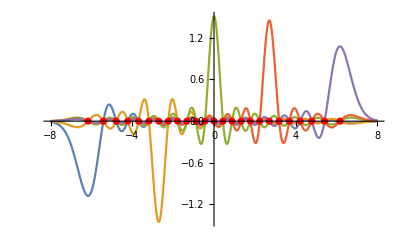

```mathematica
ohWow=
Show[
Plot[bffs[[{1, 7,13, 19, 25}]]//Evaluate, {x, -8, 8}, PlotRange->All],
ListPlot[Thread@{Flatten@haaaaar["Grid"]@"Points", 0}, PlotStyle->Red]
]
```

```mathematica
expFig[presFigFile["ho_dvr_basis"], ohWow]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/ho_dvr_basis.pdf

##### PIB

```mathematica
<<ChemTools`DVR`
```

```mathematica
hodo=ChemDVRObject["FourierDVR"]
```

ChemDVRObject[…]

```mathematica
zoop["KineticEnergy"]//MatrixPlot
```

```mathematica
zoop["PotentialEnergy"]//MinMax
```

```mathematica
zoop["Wavefunctions"][[;;3]]@"Plot"[]
```

```mathematica
zoop=
hodo[
"Points"->25,
"PotentialFunction"->(500*(.5-#)^2&),
"GridType"->{"BasisSet", "Fourier", "EchoRepresentation"->True, "GridRange"->None},
"KineticEnergyElementFunction"->{"BasisSet", "Fourier", "EchoRepresentation"->True},
"CorrectPhase"->True,
"NodelessGroundState"->True
];
```

```mathematica
xMat=SparseArray[…];
tMat=SparseArray[…];
```

```mathematica
Expand[(x-.5)^2]
```

0.25-1. x+x^2

```mathematica
blech1=
Assuming[n∈Integers&&m∈Integers,
Integrate[sinBasis[n, 1, x](x^2)sinBasis[m, 1, x], {x, 0, 1}]//Simplify
];
```

```mathematica
blech2=
Assuming[n∈Integers&&m∈Integers,
Integrate[sinBasis[n, 1, x](x^2)sinBasis[n, 1, x], {x, 0, 1}]//Simplify
];
```

```mathematica
x2Mat=Table[If[n==m, blech2, blech1], {n, 25}, {m, 25}];
```

```mathematica
vMat=.25*IdentityMatrix[25]-xMat+x2Mat;
```

```mathematica
{xGrid, transf}={Sort@#[[1]], #[[2]][[Ordering[#[[1]]]]]}&@Eigensystem[xMat];
```

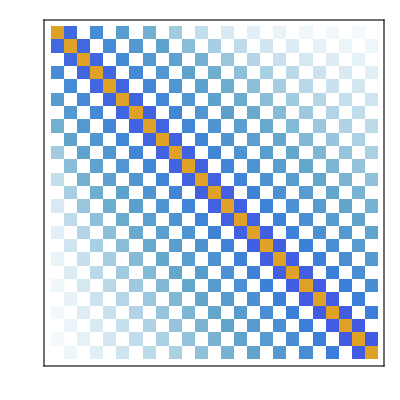
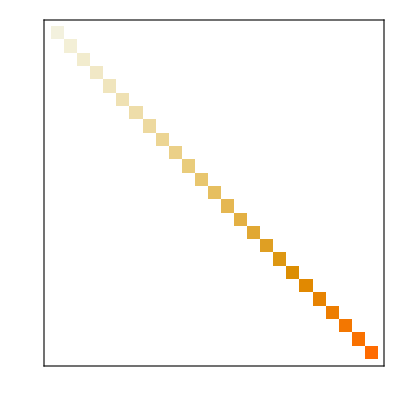
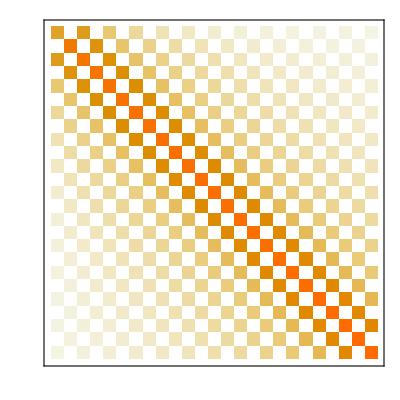
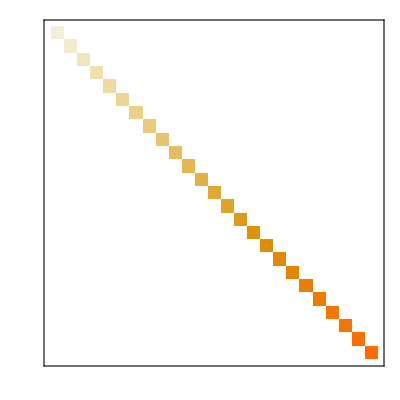
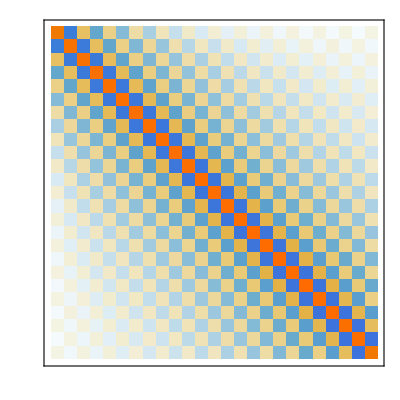
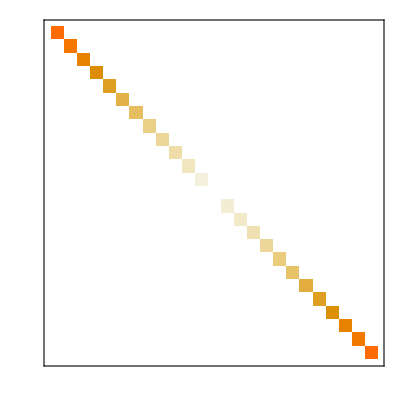
| X | T | V
PIB Basis | -Graphics- | -Graphics- | -Graphics-
DVR Basis | -Graphics- | -Graphics- | -Graphics-

```mathematica
dvrExampleGrid=
Style[
Grid[{
{"", "X", "T", "V"},
{"PIB Basis",
MatrixPlot[xMat, FrameTicks->None] ,
MatrixPlot[tMat, FrameTicks->None] , 
MatrixPlot[vMat, FrameTicks->None]
},
{"DVR Basis",
MatrixPlot[DiagonalMatrix@Sort@xGrid, FrameTicks->None] ,
MatrixPlot[Transpose[transf].tMat.transf, FrameTicks->None] , MatrixPlot[zoop["PotentialEnergy"], FrameTicks->None]
}
},
ItemSize->Full,
 Alignment->{{Right, Center, Center, Center}, Center}
],
FontFamily->"CMU Serif",
FontSize->22
]
```

```mathematica
expFig[presFigFile["dvr_example"], Pane[dvrExampleGrid, ImageSize->{700, 400}]]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/dvr_example.pdf

##### Potential Transf

```mathematica
zzz1=Eigenvectors[1/4 tMat+vMat];
```

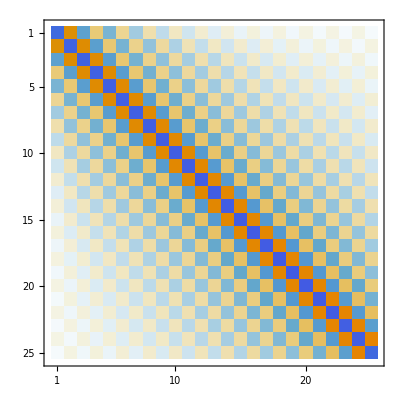

```mathematica
Transpose[zoop["Transformation"]].(tMat).zoop["Transformation"]//MatrixPlot
```

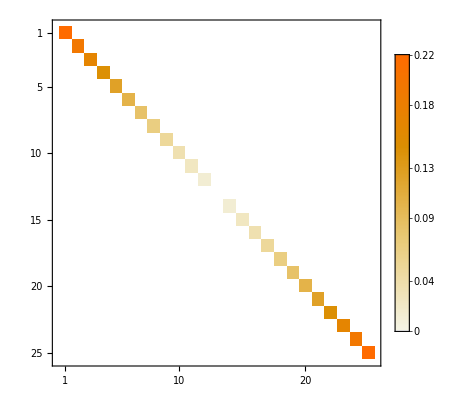

```mathematica
Round[
zoop["Transformation"].(vMat).Transpose[zoop["Transformation"]],
.005
]//MatrixPlot[#, PlotLegends->Automatic]&
```

##### Kinetic Element

T_ij = ℏ^2/(2m Δx^2)Piecewise[{{3/2 π^2, i=j}, {, }, {(2(i-j)^-1)/(i-j)^2, i≠j}}]

```mathematica
soup=Subscript[T, ij] = ℏ^2/(2m Δx^2)Piecewise[{{3/2 π^2, i=j}, {, }, {(2(i-j)^-1)/(i-j)^2, i≠j}}];
```

```mathematica
cmElement=
Graphics[
{
Inset[
MatrixPlot[zoop["KineticEnergy"], PlotRangePadding->None, FrameTicks->None, ImageSize->250],
{Left, Bottom},
{Left, Bottom}
],
Thick,
Dashed,
Line[
{
{198, 111},
{300, 225}
}
],
Line[
{
{198, 101},
{300, 25}
}
],
Inset[
Framed[
Insert[soup, 
$ops, 
{1, 1, 2}
]/.$ops:>Sequence@@{FontSize->35, FontFamily->"CMU Serif"},
 ImageSize->{450, Full},
Alignment->Center,
FrameStyle->Directive[Dashing[0], Thick, Black]
],
{300, 25},
{Left, Bottom},
{450, 200}
]
},
ImageSize->{850, 250},
PlotRange->{{0, 850}, {0, 250}}
];
```

```mathematica
expFig[presFigFile["cm_element"], Pane[cmElement,ImageSize->.8{860, 260}, Alignment->Center, ImageSizeAction->"ShrinkToFit"]
]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/cm_element.pdf

##### Grid Element

X_ij =a+ (a-b)/N Piecewise[{{i, i=j}, {, }, {0, i≠j}}]

```mathematica
xoup=Subscript[X, ij] =a+ (a-b)/N Piecewise[{{i, i=j}, {, }, {0, i≠j}}];
```

```mathematica
cmXElement=
Graphics[
{
Inset[
MatrixPlot[DiagonalMatrix@Flatten@zoop["Grid"]@"Points", PlotRangePadding->None, FrameTicks->None, ImageSize->250],
{Left, Bottom},
{Left, Bottom}
],
Thick,
Dashed,
Line[
{
{148, 111},
{300, 225}
}
],
Line[
{
{148, 101},
{300, 25}
}
],
Inset[
Framed[
Insert[xoup, 
$ops, 
{1, 1, 2}
]/.$ops:>Sequence@@{FontSize->35, FontFamily->"CMU Serif"},
 ImageSize->{450, Full},
Alignment->Center,
FrameStyle->Directive[Dashing[0], Thick, Black]
],
{300, 25},
{Left, Bottom},
{450, 200}
]
},
ImageSize->{850, 250},
PlotRange->{{0, 850}, {0, 250}}
]
```

-Graphics-

```mathematica
expFig[presFigFile["cm_x_element"], Pane[cmXElement,ImageSize->.8{860, 260}, Alignment->Center, ImageSizeAction->"ShrinkToFit"]
]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/cm_x_element.pdf

##### Expanded Wavefunctions

```mathematica
tmat=;
```

```mathematica
sinBasis[n_, l_, x_]:=√(2/(l))Sin[(x)*(π*n)/(l)]
```

```mathematica
sins=Table[sinBasis[n, 1, x], {n, 25}];
```

```mathematica
dvrBasis=#.sins&/@tmat;
```

```mathematica
normmms=NIntegrate[#.sins, {x, 0, 1}]&/@tmat;
```

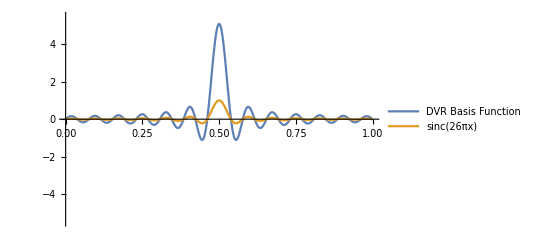

```mathematica
sincComp=
Plot[
Evaluate[
{
dvrBasis[[13]],
Sinc[26*π*(x-.5)]
}],
{x, 0, 1},
PlotStyle->{ColorData[97][1], ColorData[97][2](*Directive[Dotted, ColorData[97][2]]*)},
PlotRange->{-5.5, 5.5},
PlotLegends->
Placed[Thread@Style[{"DVR Basis Function", "sinc(26πx)"}, FontSize->18], Below],
AxesStyle->Black,
TicksStyle->Directive[FontSize->18],
Ticks->None
]
```

```mathematica
expFig[presFigFile["sinc_basis"], sincComp]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/sinc_basis.pdf

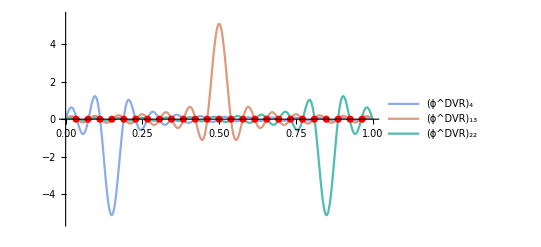

```mathematica
manyBasisFuncs=
Show[
Plot[
Evaluate[dvrBasis[[{ 4, 13, 22}]]],
{x, 0, 1},
PlotStyle->Map[ColorData[95], Range[3]],
PlotLegends->
Placed[Thread@Style[{"(ϕ^DVR)_4", "(ϕ^DVR)_13", "(ϕ^DVR)_22"}, FontSize->18], Below],
AxesStyle->Black,
TicksStyle->Directive[FontSize->18],
Ticks->None,
PlotRange->{-5.5, 5.5}
],
ListPlot[Thread[{Flatten@zoop["Grid"]@"Points", 0}], PlotStyle->Red]
]
```

```mathematica
expFig[presFigFile@"sinc_basis_funcs", manyBasisFuncs]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/sinc_basis_funcs.pdf

#### DVR 2

```mathematica
<<ChemTools`DVR`
```

```mathematica
do=ChemDVRObject["Cartesian1DDVR"];
do2=ChemDVRObject["Cartesian2DDVR"];
do3=ChemDVRObject["Cartesian3DDVR"];
```

```mathematica
littleDVRMat=do["KineticEnergy", "Points"->30]//MatrixPlot[#, ImageSize->200, FrameTicks->None]&;
biggerDVRMat=
do2["KineticEnergy", "Points"->{30, 30}]//MatrixPlot[#, ImageSize->200, FrameTicks->None]&;
biggestDVRMat=
do3["KineticEnergy", "Points"->{30, 30, 30}]//MatrixPlot[#, ImageSize->200, FrameTicks->None]&;
```

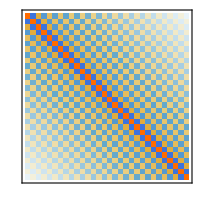

```mathematica
bigBigDVRIll=
Graphics[
{
Inset[
Show[littleDVRMat, ImageSize->200,
FrameStyle->Red, PlotRangePadding->None
],{0, 0}, {Left, Bottom}, {200, 200}],
Inset[
Show[biggerDVRMat, 
ImageSize->200,
FrameStyle->Blue, PlotRangePadding->None
],{225, 0}, {Left, Bottom}, {200, 200}],
Inset[
Show[biggestDVRMat, ImageSize->200,
FrameStyle->Darker@Green, PlotRangePadding->None
],{450, 0}, {Left, Bottom}, {200, 200}],
Dashed,
{
Red,
EdgeForm@Directive[Red, Dashed],
FaceForm@None,
Rectangle[
{226, 193},
{232, 200}
],
Line[{
{199, 2},
{225, 193}
}
],
Line[{
{199, 200},
{225, 200}
}
]
},
{
Blue,
EdgeForm@Directive[Blue, Dashed],
FaceForm@None,
Rectangle[
{225+226, 193},
{225+232, 200}
],
Line[{
{225+199, 2},
{225+225, 193}
}
],
Line[{
{225+199, 200},
{225+232, 200}
}
]
}
},
ImageSize->{650, 200},
PlotRange->{{0, 650},{0,200}}
]
```

```mathematica
expFig[presFigFile["dvr_multidim"], bigBigDVRIll]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/dvr_multidim.pdf

```mathematica
do2["KineticEnergy", "Points"->{30, 30}]["Density"]*100
```

9.75

```mathematica
do3["KineticEnergy", "Points"->{30, 30, 30}]["Density"]*100
```

0.325926

```mathematica
densityGrid=
Grid[
MapThread[
Prepend,
{
Transpose@{
{"Basis Functions (#)","", 30^1, 30^2, 30^3},
{"Matrix Elements (#)", "", 30^2,  30^4,   30^6},
{"Non-Zero Elements (%)","",  100, 9.75,  0.725}
},
{"", "", "1D", "2D", "3D"}
}
],
Alignment->Left,
Dividers->{{None, 1}, {None, 1}}
]
```

| Basis Functions (#) | Matrix Elements (#) | Non-Zero Elements (%)
 |  |  | 
1D | 30 | 900 | 100
2D | 900 | 810000 | 9.75
3D | 27000 | 729000000 | 0.725

```mathematica
Style[densityGrid, FontFamily->"CMU Serif"]
```

| Basis Functions (#) | Matrix Elements (#) | Non-Zero Elements (%)
 |  |  | 
1D | 30 | 900 | 100
2D | 900 | 810000 | 9.75
3D | 27000 | 729000000 | 0.725

```mathematica
expFig[presFigFile@"dvr_multidim_stats", 
Style[densityGrid, FontFamily->"CMU Serif"],
ImageSize->{600, 100}
]
```

$Failed

#### Other Project

#### H5+

```mathematica
<<ChemTools`Objects`
<<ChemTools`Objects`ObjectFramework`
<<ChemTools`Objects`Utilities`
<<ChemTools`Data`
```

```mathematica
ChemRemove[h5];
```

```mathematica
h5=CreateGeometricAtomset["BowtieD2D",ConstantArray["H", 5]];
```

```mathematica
AtomColor[h5["Atoms"]]=Darker/@{Green, Red, Red, Blue, Blue}
```

```mathematica
atoms=h5["Atoms"];
bonds=h5["Bonds"];
```

```mathematica
view1=h5["View"][Method->{"ShrinkWrap"->True}];
```

```mathematica
atoms[[1]]["Move"][{.5, 0, 0}];
bonds[[3]]["Break"][];
bonds[[4]]["Break"][];
```

```mathematica
view2=h5["View"][Method->{"ShrinkWrap"->True}];
```

```mathematica
pos1=atoms[[1]]["Position"];
pos2=atoms[[2]]["Position"];
pos3=atoms[[3]]["Position"];
atoms[[1]]["Move"][pos3, "Set"]
atoms[[2]]["Move"][ pos1 , "Set"]
atoms[[3]]["Move"][ pos2 , "Set"]
```

```mathematica
view3=h5["View"][Method->{"ShrinkWrap"->True}];
```

```mathematica
atoms[[2]]["Move"][{-.5, 0, 0}];
AtomAddBond[atoms[[2]], CreateBond[atoms[[2]], atoms[[4]], 1]]
AtomAddBond[atoms[[2]], CreateBond[atoms[[2]], atoms[[5]], 1]]
```

```mathematica
view4=h5["View"][Method->{"ShrinkWrap"->True}];
```

```mathematica
doubleArrows=
{
Polygon[
{
{0, .01},
{1, .01},
{.7, .3},
{.8, .06},
{0, .06},
{0, .01}
}
],
Polygon[
{
{1, -.01},
{0, -.01},
{.3, -.3},
{.2, -.06},
{1, -.06},
{1, -.01}
}
]
};
```

```mathematica
rotMode=
Grid[
{
{Show[view1, ViewPoint->{0, -2, 1}, ImageSize->200], 
Graphics[doubleArrows, ImageSize->50], 
Show[view2, ViewPoint->{0, -2, 1}, ImageSize->200]},
{Null, Null, Graphics[GeometricTransformation[doubleArrows, RotationTransform[90 Degree]], ImageSize->{Automatic, 50}]},
{Show[view4, ViewPoint->{0, -2, 1}, ImageSize->200], Graphics[doubleArrows, ImageSize->50], Show[view3, ViewPoint->{0, -2, 1}, ImageSize->200]}
},
Alignment->Center
];
```

```mathematica
Export[
presFigFile["h5+_rot.png"],
rotMode//Rasterize[#, Background->None, ImageResolution->225]&
]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/h5+_rot.png

```mathematica
Export[
presFigFile["h5+"],
h5["View"][
"AtomColor"->Directive[GrayLevel[.8], Glow[Black]],
 Method->{"ShrinkWrap"->True}
]//Rasterize[#, Background->None, ImageResolution->225]&
]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/h5+.pdf

##### Permutations

##### Coordinate System

```mathematica
Show[
h5["View"]["AtomColor"->Directive[GrayLevel[.8], Glow[Black]], Method->{"ShrinkWrap"->True}],
Graphics3D[
{
Black,
AbsoluteThickness[1],
Arrowheads[{-.025, .025}],
Text[Style["R_1", 16], {-.9, 0, .15}],
Arrow[{{-1.4 ,0, 0}, {-.3, 0, 0}}],
Text[Style["R_2", 16], {1, 0, .15}],
Arrow[{{1.4 ,0, 0}, {.3, 0, 0}}],
Text[Style["r_1", 16], {.2+3/2, 0, 0}],
Arrow[{{.1+3/2,-.65 , 0}, {.1+3/2, .55, 0}}],
Text[Style["r_2", 16], {-(.25+3/2), 0, 0}],
Arrow[{{-(.125+3/2),0,-.68 }, {-(.125+3/2), 0,.58}}],
White,
Point[{-(.4+3/2),0,0 }]
}
]
]//Rasterize[#, ImageResolution->225, Background->None]&
```

-Graphics-

```mathematica
expFig["h5geom", Cell@BoxData@PaneBox[NotebookRead[PreviousCell[]][[1, 1]], ImageSize->500, ImageSizeAction->"ShrinkToFit"]]
```

/Users/Mark/Documents/UW/Research/Second Year/Research Summary/figures/h5geom.pdf

```mathematica
Show[
h5["View"]["AtomColor"->Directive[GrayLevel[.8], Glow[Black]], Method->{"ShrinkWrap"->True}],
Graphics3D[
{
Black,
AbsoluteThickness[1],
Arrowheads[{-.025, .025}, Appearance->"Projected"],
Arrow[{{3/2,-1.5 , 0}, {3/2, 1.5, 0}}],
Arrow[{{-(3/2),0,-1.5 }, {-(3/2), 0,1.5}}],
White,
Point[{-(.4+3/2),0,0 }]
}
]
]//Rasterize[#, ImageResolution->225, Background->None]&
```

-Graphics-

#### Shared Proton

Ĥ=(1/m_H_2+2/m_H)p_a^2+1/m_H_2 p_s+V(s, a)

```mathematica
-Graphics-//ImageCrop
```

-Graphics-

```mathematica
Grid@{
{"s (Å)", -Graphics-},
{"", "a (Å)"}
}//Style[#,FontFamily->"CMU Serif"]&//Rasterize[#, ImageResolution->225]&
```

-Graphics-

#### H2

Ĥ(r_1, r_2)=1/m_H_2 p_r_1^2+1/m_H_2 p_r_2^2+V(r_1, r_2)

```mathematica
-Graphics-//ImageCrop
```

-Graphics-

```mathematica
Grid@{
{"r_1 (Å)", -Graphics-},
{"", "r_2 (Å)"}
}//Style[#,FontFamily->"CMU Serif"]&//Rasterize[#, ImageResolution->225]&
```

-Graphics-

#### 4D

Ĥ(s, a, r_1, r_2)=(1/m_H_2+2/m_H)p_a^2+1/m_H_2 p_s+1/m_H_2 p_r_1^2+1/m_H_2 p_r_2^2+V(s, a, r_1, r_2)
=(T̂)_(s,a)+(T̂)_(r_1,r_2)+V(s, a, r_1, r_2)

```mathematica
-Graphics-//ImageCrop
```

-Graphics-

```mathematica
-Graphics-//ImageCrop
```

-Graphics-

ϕ_(n_s, n_a, n_(r_1,)n_r_2)=ϕ_n_sϕ_n_aϕ_n_r_1ϕ_n_r_2

```mathematica
-Graphics-//ImageCrop
```

-Graphics-

#### Adiabatic

##### Energy Table

```mathematica
eesHP=
#-#[[1]]&@
hpWavefunctions["Wavefunctions"]["Energies"]
```

{0.,529.954,861.997,1244.53,1472.51,1815.26,1868.72,2125.62,2274.19,2458.58,2633.59,2742.29,2889.14,2950.82,2975.02,3110.61,3126.98,3268.61,3321.7,3453.52,3554.57,3642.88,3791.37,3814.79,3893.06}

```mathematica
h2TestWfns=
Import["~/Documents/UW/Research/H5+/results/h2SAWavefunctions_2.mx"];
```

```mathematica
eesH2=
#-#[[1]]&@
h2TestWfns[[1751]]["Energies"]
```

{0.,3389.67,3464.88,6749.3,6807.01,6906.95,10076.6,10139.9,10215.,10325.3}

```mathematica
eeGrid=
Grid[
Prepend[
MapIndexed[
{Row@{Style["n", Italic], "=", #2[[1]]-1},formatNumber[eesHP[[#2[[1]]]], 2],  formatNumber[#, 2]} &,
eesH2
],
{"", 
Row@{
Subscript[Superscript["ℰ",Row@{"(",Style["n", Italic], ")"}], "H+"],
" (",
Superscript["cm", -1],
")"
}, 
Row@{
Subscript[Superscript["ℰ", Row@{"(",Style["n", Italic], ")"}], Subscript["H", 2]],
" (",
Superscript["cm", -1],
")"
}}
],
Alignment->{
{"=", Right, Right}, 
{}
},
Dividers->{{None, 1, GrayLevel[.95]}, {None, 1} }
]//Style[#, FontFamily->"CMU Serif"]&;
```

```mathematica
expFig[presFigFile["E_grid"],Pane[eeGrid,{170,189}, ImageSizeAction->"ResizeToFit"]]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/E_grid.pdf

##### Shared Proton Plots

```mathematica
hpWavefunctions=Import@"~/Documents/UW/Research/H5+/results/hp_wfns_anne.mx";
```

```mathematica
h5pWfnPlots=
With[{min=-.21, max=.21, ncontours=20, dropRight=2, dropLeft=1},
With[{step=(max-min)/(ncontours+If[EvenQ[ncontours], 1, 0])},
hpWavefunctions["Wavefunctions"][[;;8]]@"Plot"[
"PlotMode"->"Contour", "PlotDisplayMode"->"List",
Contours->Range[min, max, step],
ContourShading->
Map[
If[.5-dropLeft/ncontours<=#<=.5+dropRight/ncontours,
 White, 
ColorData["RedBlueTones"]@#
]&,
Rescale@ Range[min, max, step]
],
RegionFunction->(regMem[{#, #2}]&),
PlotRange->Append[RegionBounds[axesReg], {min, max}],
PlotRangePadding->None,
Frame->None,
ContourStyle->None(*Directive[Thick, Opacity[.25, Gray]]*),
ContourLabels->None,
ImageSize->200,
Epilog->{EdgeForm[Black], axesGraphics, 
Text[Style[figStyleText@"R_1", 24], RegionCentroid@axesGraphics[[1]], {1, 1}],
Text[Style[figStyleText@"R_2", 24], RegionCentroid@axesGraphics[[2]], {-1, 1}]
}
]
]
];
```

```mathematica
h5pWfnGrid=Map[Show[#,  Method->{"ShrinkWrap"->True}]&, DeleteCases[h5pWfnPlots, {___, White, ___}, ∞]]//Thread//Partition[#, 4]&//Grid;
```

```mathematica
expFig[presFigFile["h5p_wfns"],h5pWfnGrid]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/h5p_wfns.pdf

##### H2 Plots

```mathematica
mean[[{3}]]@"Plot"[]
```

```mathematica
MinMax/@mean["Wavefunctions"][[;;8]]//MinMax
```

```mathematica
h2WfnPlots=
With[{min=-.11, max=.11, ncontours=20,  dropRight=2, dropLeft=1},
With[{step=(max-min)/(ncontours+If[EvenQ@ncontours, 1, 0])},
mean[[;;8]]@"Plot"[
"PlotMode"->"Contour", "PlotDisplayMode"->"List",
Contours->Range[min, max, step],
ContourShading->
Map[
If[.5-dropLeft/ncontours<=#<=.5+dropRight/ncontours,
 White, 
ColorData["RedBlueTones"]@#
]&,
Rescale@ Range[min, max, step]
],
RegionFunction->((#<.8&&#2<.8&)),
PlotRange->{{All, .8}, {All, .8}, {min, max}},
PlotRangePadding->None,
Frame->None,
ContourStyle->None(*Directive[Thick, Opacity[.25, Gray]]*),
ContourLabels->None,
ImageSize->200
]
]
];
```

```mathematica
h2WfsForPlots=
Show[
Graphics[GeometricTransformation[#[[1]], RotationTransform[π/4]]],
Graphics@{
EdgeForm[Black], axesGraphics2, 
Text[Style[figStyleText@"r_1", 24], RegionCentroid@axesGraphics2[[1]], {1, 1}],
Text[Style[figStyleText@"r_2", 24], RegionCentroid@axesGraphics2[[2]], {-1, 1}]
},
Method->{"ShrinkWrap"->True}
]&/@h2WfnPlots;
```

```mathematica
h2WfsGrid=DeleteCases[h2WfsForPlots, {___, White, ___}, ∞]//Partition[#, 4]&//Grid
```

```mathematica
expFig[presFigFile["h2_wfns"], h2WfsGrid]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/h2_wfns.pdf

##### Stuff

Ĥ(s, a; n_(r_1,)n_r_2)=ϕ(r_1, r_2; s, a)(T̂)_(s,a)+(T̂)_(r_1,r_2)+V(s, a, r_1, r_2)ϕ(r_1, r_2; s, a)
=(T̂)_(s,a)+(ĥ)_(r_1,r_2)(s, a)

```mathematica
-Graphics-//ImageCrop
```

-Graphics-

```mathematica
h2SAWavefunctions=Import@"~/Documents/UW/Research/H5+/h2_outer_SA_wfns.mx";
```

```mathematica
h2AdiabatInterps=;
```

```mathematica
Plot[#[0, s]&/@h2AdiabatInterps//Evaluate, 
{s, 1.2, 2.2},
Frame->True,
 FrameLabel->{"s (Å)", "V(s, a=0) (cm^-1)"},
FrameStyle->Directive[Black],
BaseStyle->{FontSize->25, FontFamily->"CMU Serif"},
PlotRange->{{1.2, 2.2}, {0, 25000}},
FrameTicks->{
{Map[{#, #, {.01,0}, {}}&]@Range[3000, 15000, 3000], None}, 
{Map[{#, #, {.01,0}, {}}&]@Range[.8, 4.5, .1], None}
},
 ExclusionsStyle->None,
ImageSize->{Automatic, 450}
];
```

```mathematica
minMaxes={2780+{0, 250},6000+{0, 250},9250+{0, 250}};
xyDoop=.005+{1.50, 1.52};
littlePlots=
MapThread[
Plot[#[0, s]&/@h2AdiabatInterps[[#]]//Evaluate, {s, 1.50, 1.55},
Frame->True,
FrameLabel->{None, None},
FrameStyle->Black(*Directive[Echo@ColorData[97][#[[1]]]]*),
PlotStyle->Thread@Directive[AbsoluteThickness[3], ColorData[97]/@#],
BaseStyle->{FontSize->20, FontFamily->"CMU Serif"},
PlotRange->{xyDoop, #2},
FrameTicks->{
{Map[{#, #, {.01,0}, {}}&]@#3, None}, 
{Map[{#, #, {.01,0}, {}}&]@{1.5075, 1.515, 1.5225}, None}
},
 ExclusionsStyle->None,
ImageSize->{Automatic, 150}
]&,
{
{{1},{2, 3},{4, 5, 6}},
minMaxes,
{
minMaxes[[1, 1]]+65*{1, 2 ,3},
minMaxes[[2, 1]]+65*{1, 2 ,3},
minMaxes[[3, 1]]+65*{1, 2 ,3}
}
}
];
```

```mathematica
middlePlot=
Plot[#[0, s]&/@h2AdiabatInterps//Evaluate,
 {s, 1.44, 1.59},
PlotStyle->AbsoluteThickness[3],
Frame->True,
 FrameLabel->{"s (Å)", "V(s, a=0) (cm^-1)"},
FrameStyle->Directive[Black],
BaseStyle->{FontSize->25, FontFamily->"CMU Serif"},
PlotRange->{{1.44, 1.59}, {2500, 10000}},
FrameTicks->{
{Map[{#, #, {.01,0}, {}}&]@Range[3000, 15000, 3000], None}, 
{Map[{#, #, {.01,0}, {}}&]@{1.45, 1.50, 1.55}, None}
},
 ExclusionsStyle->None,
ImageSize->{Automatic, 450}
];
```

```mathematica
extraDist=1.1;
boxBigness=.2;
extraHeights=
{
boxBigness*{-1, 1}+.05,
boxBigness*{-1, 1}+.5,
boxBigness*{-1, 1}+.95
};
lineColors=
ColorData[97]/@{1, 3, 4};
{littleMiddlelines, {littleLinePos}}=
Reap[
MapThread[
{
EdgeForm[Black],
FaceForm[None],
Rectangle@@Transpose[{xyDoop, #}],
Thick,
Dashed,
#3,
Line@
Sow@Thread[
{
Thread[{xyDoop[[2]], #}],
Thread[
{
Rescale[extraDist,  {0, 1}, PlotRange[middlePlot][[1]] ], 
Rescale[#2, {0, 1}, PlotRange[middlePlot][[2]] ]
}]
}
]
}&,
{
minMaxes,
extraHeights,
lineColors
}
]
];
boxXYScale={1, 1};
cbox=
#+
{{0, 1}, {-.75, 0}}*
MinMax[
{
Subtract@@#[[1, {2, 1}, 1]], 
(Subtract@@#[[{2, 1}, 2, 2]])
}&/@littleLinePos
]+{{-.2(Subtract@@#[[1,{2,1}]]), 0}, {0, 0}}&@CoordinateBoundingBox[
Prepend[littleLinePos, PlotRange[middlePlot]]
];
```

```mathematica
omgThisSuckedSoMuch=
Graphics[
{
Inset[
Show[ReplacePart[middlePlot, 1->{}], AspectRatio->Full],
{#[[1, 1]], Mean@#[[2]]}&@PlotRange[middlePlot],
Scaled[{.01, .5}],
Scaled[{.66, .8}]
],
middlePlot[[1]],
littleMiddlelines,
MapThread[
Inset[
Framed[
Show[#, AspectRatio->Full, ImageSize->Full],
FrameStyle->Directive[Thick, #3],
 FrameMargins->15
],
#2[[2, 2]], 
Scaled[{0, 1}],
{
(Subtract@@PlotRange[middlePlot][[1, {2, 1}]])*
(Subtract@@#2[[{2, 1}, 2, 2]])/
(Subtract@@PlotRange[middlePlot][[2, {2, 1}]]), 
Subtract@@#2[[{2, 1}, 2, 2]]
}
]&,
{
littlePlots,
littleLinePos,
lineColors
}
]
},
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic, 750},
PlotRange->cbox
]
```

-Graphics-

```mathematica
expFig[presFigFile["holy_shit_why"], Pane[omgThisSuckedSoMuch, {Automatic, 450}, ImageSizeAction->"ShrinkToFit"]]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/holy_shit_why.pdf

```mathematica
changePDFMargins[presFigFile["holy_shit_why"], {500, 500}, {-200, 100}, 10]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/holy_shit_why.pdf

```mathematica
(Subtract@@cbox[[2, {2, 1}]])/10000
```

1.15125

```mathematica
littleLinePos
```

{{{{1.525,2780},{1.5975,1750.}},{{1.525,3030},{1.5975,4000.}}},{{{1.525,6000},{1.5975,5125.}},{{1.525,6250},{1.5975,7375.}}},{{{1.525,9250},{1.5975,8500.}},{{1.525,9500},{1.5975,10750.}}}}

```mathematica
CoordinateBoundingBox[
Join[
Prepend[littleLinePos, PlotRange[middlePlot]],
1.45*
{
Subtract@@#[[1, {2, 1}, 1]], 
(Subtract@@#[[{2, 1}, 2, 2]])
}&/@littleLinePos
]
]
```

{{0.105125,1.59},{2500.,10750.}}

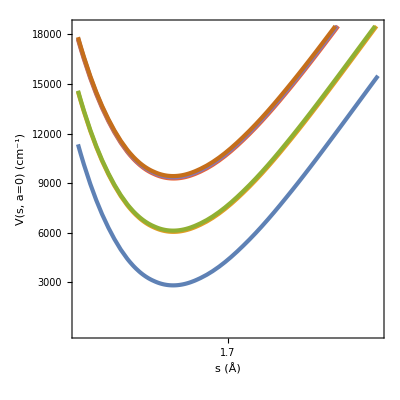

```mathematica
bigPlot=
Plot[#[0, s]&/@h2AdiabatInterps//Evaluate, 
{s, 1.2, 2.2},
PlotStyle->AbsoluteThickness[3],
Frame->True,
 FrameLabel->{"s (Å)", "V(s, a=0) (cm^-1)"},
FrameStyle->Directive[Black],
BaseStyle->{FontSize->25, FontFamily->"CMU Serif"},
PlotRange->{{1.2, 2.2}, {0, 18500}},
FrameTicks->{
{Map[{#, #, {.01,0}, {}}&]@Range[3000, 25000, 3000], None}, 
{Map[{#, #, {.01,0}, {}}&]@Range[.8, 4.5, .225], None}
},
 ExclusionsStyle->None,
ImageSize->{Automatic, 450},
AspectRatio->1
]
```

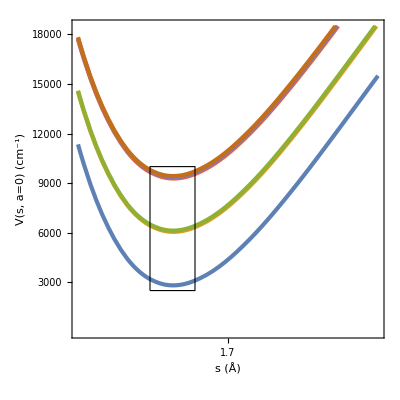

```mathematica
bigPlotWithStuff=
Show[
bigPlot,
AspectRatio->1,
Epilog->{
EdgeForm[Black],
FaceForm[None],
Rectangle[{1.44,2500},{1.59,  10000}]
(*Inset[
Show[middlePlot, FrameTicks->None, FrameLabel->None, AspectRatio->Full], 
{Mean@{1.44,1.59}-.15,14000},
{Left, Bottom},
 {.45, 10000}
],
Dashed,
Thick,
Line[
{
{1.44, 10000},
 {Mean@{1.44,1.59}-.15,14000}
}
],
Line[
{
{1.59, 10000},
 {Mean@{1.44,1.59}-.15+.45,14000}
}
]*)
}
]
```

```mathematica
expFig[presFigFile@"adiabats", bigPlotWithStuff]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/adiabats.pdf

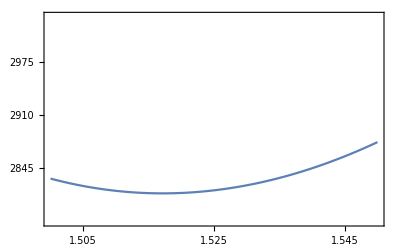
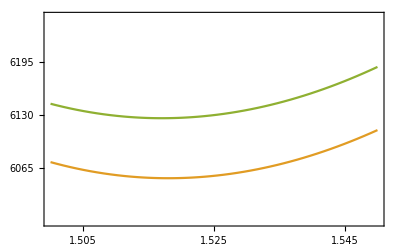
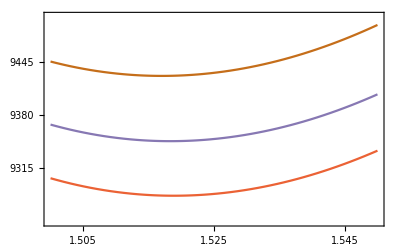

```mathematica
adiabatSubFig=
MapThread[
Plot[#[0, s]&/@h2AdiabatInterps[[#]]//Evaluate, {s, 1.50, 1.55},
Frame->True,
 FrameLabel->{None, None},
FrameStyle->Directive[Black],
PlotStyle->(ColorData[97]/@#),
BaseStyle->{FontSize->20, FontFamily->"CMU Serif"},
PlotRange->{{1.50, 1.55}, #2},
FrameTicks->{
{Map[{#, #, {.01,0}, {}}&]@#3, None}, 
{Map[{#, #, {.01,0}, {}}&]@{1.505, 1.525, 1.545}, None}
},
 ExclusionsStyle->None,
ImageSize->{Automatic, 150}
]&,
{
{{1},{2, 3},{4, 5, 6}},
{2780+{0, 250},6000+{0, 250},9250+{0, 250}},
{
2780+65*{1, 2 ,3},
6000+65*{1, 2 ,3},
9250+65*{1, 2 ,3}
}
}
]
```

#### Contracted

Ĥ(s, a, r_1, r_2)=(T̂)_(s,a)+(T̂)_(r_1,r_2)+V(s, a, r_1, r_2)
=(T̂)_(s,a)+(T̂)_(r_1,r_2)+V_(s=s_e,a=a_e)(r_1, r_2)+V_c(s, a, r_1, r_2)
=(T̂)_(s,a)+(ĥ)_(r_1,r_2)+V_c(s, a, r_1, r_2)

```mathematica
-Graphics-//ImageCrop
```

ϕ_(n_s, n_a, n_(r_1,)n_r_2)=ϕ_n_sϕ_n_aϕ_(n_(r_1,)n_r_2)

```mathematica
-Graphics-//ImageCrop
```

-Graphics-

H(s, a, r_1, r_2)=T_(s,a)⊕h_(r_1,r_2)+V_c

```mathematica
-Graphics-//ImageCrop
```

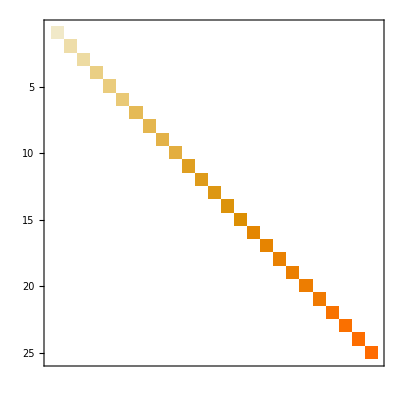
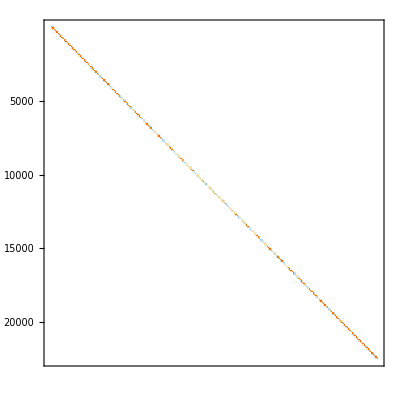
```mathematica
Grid[{
{"T_(s, a):", -Graphics-, "h_r_1:", -Graphics-},
{"V_c:", -Graphics-, "H:", -Graphics-}


}, Alignment->Right]//Style[#, FontFamily->"CMU Serif"]&//Rasterize[#, ImageResolution->225, Background->None]&
```

### Projections

```mathematica
<<ChemTools`Wavefunctions`
WavefunctionsObject;
```

```mathematica
reg=TransformedRegion[Rectangle[{.6, .6}, {3.4, 3.4}], RotationTransform[π/4]];
regMem=RegionMember[reg];
axesReg=RegionResize[reg, Scaled[1.1]];
axesGraphics=
{
RegionBoundary[axesReg][[;;, {1, 2}]],
RegionBoundary[axesReg][[;;, {4, 5}]]
};
reg2=TransformedRegion[Rectangle[{.3, .3}, {1., 1.}], RotationTransform[π/4]];
regMem2=RegionMember[reg2];
axesReg2=RegionResize[reg2, Scaled[1.1]];
axesGraphics2=
{
RegionBoundary[axesReg2][[;;, {1, 2}]],
RegionBoundary[axesReg2][[;;, {4, 5}]]
};
```

```mathematica
h2Wfns=WavefunctionsObject[…];
```

```mathematica
gsWfns=;
state2=;
state3=;
```

```mathematica
lh=WavefunctionsObject[…];
rh=WavefunctionsObject[…];
```

```mathematica
mean=
WavefunctionsObject[
{
rh["Energies"][[;;10]],
MapThread[
ChemTools`DataStructures`Package`GFAdd[
Scale[#, .5],
Scale[#2, .5]
]&,
{lh["Wavefunctions"][[;;10]], rh["Wavefunctions"][[;;10]]}
]
},
rh["Grid"]
];
```

```mathematica
baseh2wfPlots=
mean[[;;6]]@"Plot"[
"PlotMode"->"Contour", "PlotDisplayMode"->"List", ColorFunction->ColorData[{"ThermometerColors", {.1, 1}}],
Contours->Range[-.12, .12, .01],
ContourShading->
Map[
If[.5-.001<=#<.5+.08, Opacity[0.], ColorData["ThermometerColors"]@#]&,
Rescale@ Range[-.12, .12, .01]
],
RegionFunction->(#<.7&&#2<.7&),(*
PlotRange->{{All, .7}, {All, .7}},*)
PlotRangePadding->None,
Frame->None,
ContourStyle->None(*Directive[Thick, Opacity[.25, Gray]]*),
ContourLabels->None,
ImageSize->200
];
```

```mathematica
h2WfsForPlots=
Show[
Graphics[GeometricTransformation[#[[1]], RotationTransform[π/4]]],
Graphics@{
EdgeForm[Black], axesGraphics2, 
Text[Style[figStyleText@"r_1", 24], RegionCentroid@axesGraphics2[[1]], {1, 1}],
Text[Style[figStyleText@"r_2", 24], RegionCentroid@axesGraphics2[[2]], {-1, 1}]
}
]&/@baseh2wfPlots[[;;6]];
```

```mathematica
projWfs=;
projWf456=;
```

```mathematica
plotWfs//Clear
plotWfs[wfs_, min_, max_, ncontours_, ops___]:=
With[{step=(max-min)/(ncontours+If[EvenQ[ncontours], 1, 0]), dropRight=2, dropLeft=1},
wfs@"Plot"[
"PlotMode"->"Contour", "PlotDisplayMode"->"List",
ops,
Contours->Range[min, max, step],
ContourShading->
Map[
If[.5-dropLeft/ncontours<=#<=.5+dropRight/ncontours,
 White, 
ColorData["RedBlueTones"]@#
]&,
Rescale@ Range[min, max, step]
],
PlotRange->Append[RegionBounds[axesReg], {min, max}],
PlotRangePadding->None,
Frame->None,
ContourStyle->None(*Directive[Thick, Opacity[.25, Gray]]*),
ContourLabels->None,
ImageSize->200
]
]
plotTheseWfs[min_, max_, ncontours_][wfs_]:=
plotWfs[
wfs,
min, max, ncontours,
RegionFunction->(regMem[{#, #2}]&),
Epilog->{EdgeForm[Black], axesGraphics, 
Text[Style[figStyleText@"R_1", 24], RegionCentroid@axesGraphics[[1]], {1, 1}],
Text[Style[figStyleText@"R_2", 24], RegionCentroid@axesGraphics[[2]], {-1, 1}]
}
]
```

```mathematica
gsWfPlots=
plotTheseWfs[-.25, .25, 30][gsWfns];
```

```mathematica
gsPlotSels=
Pick[
Range[25],
sadSpec["Intensities"][[;;25]]-.001//UnitStep,
1
];
```

```mathematica
gsPlotsBlots=
gsWfPlots[[gsPlotSels]];
```

```mathematica
lowerStateToPlot=
plotTheseWfs[-.25, .25, 30]@
projWfs[[1]][[;;20]];
```

```mathematica
projWfs2=
WavefunctionsObject[
{
projWfs[[2]]["Energies"],
Head[#][projWfs[[1]]["Grid"], #["Values"]]&/@
projWfs[[2]]["Wavefunctions"]
},
projWfs[[1]]["Grid"]
];
```

```mathematica
upperStateToPlot=
plotTheseWfs[-.25, .25, 30]@
projWfs2[[;;20]];
```

```mathematica
lowerStateHBasis=
plotTheseWfs[-.25, .25, 30][state2[[;;10]]];
```

```mathematica
upperStateHBasis=
plotTheseWfs[-.25, .25, 30][state3[[;;10]]];
```

```mathematica
plotSelections456=
Pick[
Range[25],
sadSpec["Intensities"][[51;;]]-10^-4//UnitStep,
1
][[;;3]];
```

```mathematica
toPlot456=
plotTheseWfs[-.25, .25, 30][#[[plotSelections456]]]&/@projWf456;
```

```mathematica
arrangePlots//Clear
arrangePlots[p1_, p2_, qns_]:=
Graphics[
{
Inset[
Show[
DeleteCases[
#,
{___, White, ___},
∞
],
PlotRange->RegionBounds@axesReg-{0, .1}
]&@p1,
{0, Bottom},{0, Bottom},
Alignment->{Center, Top}
],
Text[Hold@qns,{100, 200},{-1, 1}],
Inset[
Magnify[
Show[
DeleteCases[
#,
{___, White, ___},
∞
],
ImageSize->150,
Method->{"ShrinkWrap"->True}
]&@p2,.75],
{-100, Top},
{Right, Top} ,
Alignment->{Left, Top}
]
(*Inset[
Magnify[
Show[
DeleteCases[
#,
{___, White, ___},
∞
],
ImageSize->150
]&@p3,.75],
 {Right, Top},
{Right, Center},
Alignment->{Right, Top}
]*)
}/.{
Text[Hold[a_], b___]:>Text[a, b],
Text[a_, b___]:>Text[figStyleText@a, b]
},
PlotRange->{450*{-1/2, 1/2}, {0, 200}},
ImageSize->{450, 150},(*
Method->{"ShrinkWrap"->False},*)
AspectRatio->Full
]
```

```mathematica
actualPlots=
MapThread[
{
arrangePlots[lowerStateToPlot[[#]], 
h2WfsForPlots[[2]], 
figStyleText@stateBraKets[[1, #]]
],
 arrangePlots[upperStateToPlot[[#]], h2WfsForPlots[[3]],
figStyleText@stateBraKets[[2, #]]
]
}&,
Transpose@statesToPlot
];
```

```mathematica
statesToPlotNumbers=
Pick[
Range[25],
sadSpec["Intensities"][[26;;50]]-10^-3//UnitStep,
1
]
```

{1,4,5,8,9,12,13,15,17,20}

```mathematica
statesToPlot=
{
{1, 1, 2},
{4, 3, 2},
{5, 3, 4},
{8, 5, 4},
{12, 5, 6},
{13, 7, 6},
{15, 8, 6},
{17, None, None},
{20, 10, 9}
};
```

```mathematica
betterStateDivisions=
{

{0,1,1,{2, "But weird"},2,3,3,{2,Positive},4,6,{2,Negative},{6,Subtract,7},{6,Plus,7},"No Clue",7,{3,Positive},9,8,{4,Negative},{4,Positive}},

{1,0,{0, "Expanded"},1,{1, "Expanded"},2,
{2, "Expanded"},3,{3, "Expanded"},{4, "Expanded"},4,5,{2.5,Positive},6,{5, "But weird"},"No Clue",{3.5,Positive},7,8,8}
};
```

```mathematica
parseStateThing//Clear
parseStateThing[i_Integer]:=Ket[i];
parseStateThing["No Clue"]:="???";
parseStateThing[{i_, Positive}]:=Subscript[Ket[Round@i, 0], "+"];
parseStateThing[{i_, Negative}]:=Subscript[Ket[Round@i, 0], "-"];
parseStateThing[{i_, _String}]:=Superscript[Ket[Round@i], "′"];
parseStateThing[{n_, Plus, m_}]:=Ket[Row@{Round[n], "+", Round[m]}];
parseStateThing[{n_, Subtract, m_}]:=Ket[Row@{Round[n], "-", Round[m]}];
```

```mathematica
stateBraKets=
MapThread[
With[{key=#},
Map[Row@{Ket[key], parseStateThing[#]}&, #2]
]&,
{
{"A", "S"},
betterStateDivisions
}
];
```

```mathematica
actualPlots=
MapThread[
{
arrangePlots[lowerStateToPlot[[#]], 
h2WfsForPlots[[2]], 
figStyleText@stateBraKets[[1, #]]
],
 arrangePlots[upperStateToPlot[[#]], h2WfsForPlots[[3]],
figStyleText@stateBraKets[[2, #]]
]
}&,
Transpose@statesToPlot
];
```

```mathematica
fullWfGrid1=Grid@actualPlots[[;;4]];
fullWfGrid2=Grid@actualPlots[[5;;]];
```

```mathematica
wfnsGridExample=
Grid[
Prepend[{Null, figStyleText@Style["Anti-Symmetric Adiabat A", 18],figStyleText@Style["Symmetric Adiabat S", 18]}]@
MapThread[
Prepend[#,
 figStyleText@
Style[Row@{"ω", "=", #2, " ","(", Superscript["cm", -1], ")"}, 18]
]&,
{
actualPlots[[{1,2,  -1}]],
Round@{3370.3929426771356,3863.2294338151696,5637.909087845008}
}
],
Spacings->{2, 2},
ItemSize->{{All, 35, 35}, Automatic},
 Dividers->{{None, GrayLevel[.8], GrayLevel[.8]}, {None, {Black}, None}}
];
```

```mathematica
expFig[presFigFile@"wavefunctions", 
Pane[wfnsGridExample, {650, Automatic}, 
ImageSizeAction->"ResizeToFit"
]
]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/wavefunctions.pdf

```mathematica
stateChops=Partition[statesToPlot[[All, 1]], UpTo@3];
meeeeeeh=sadSpec["Frequencies"][[26;;]][[#]]&/@stateChops;
```

```mathematica
wfnsGridExamples2=
MapThread[
Grid[
Prepend[{Null, 
figStyleText@Style["Anti-Symmetric Adiabat A", 18],figStyleText@Style[ "Symmetric Adiabat S",  18]}]@
MapThread[
Prepend[#,
 figStyleText@
Style[Row@{"ω", "=", #2, " ","(", Superscript["cm", -1], ")"}, 18]
]&,
{
#,
Round@#2
}
],
Spacings->{2, 2},
ItemSize->{{All, All, All}, Automatic},
 Dividers->{{None, GrayLevel[.8], GrayLevel[.8]}, {None,{Black}, None}}
]&,
{
Partition[actualPlots, UpTo[3]],
meeeeeeh
}
];
```

```mathematica
MapIndexed[
expFig[
"wavefunctions_table_"<>ToString[#2[[1]]], 
Pane[#, {650, Automatic}, 
ImageSizeAction->"ResizeToFit"
]
]&,
wfnsGridExamples2
]
```

{/Users/Mark/Documents/UW/Research/Second Year/Research Summary/figures/wavefunctions_table_1.pdf,/Users/Mark/Documents/UW/Research/Second Year/Research Summary/figures/wavefunctions_table_2.pdf,/Users/Mark/Documents/UW/Research/Second Year/Research Summary/figures/wavefunctions_table_3.pdf}

```mathematica
baseStates456=
{
{1, 3, 3},
{0, {2, "But weird"}, 2},
{1, 1, 3}
};
states456=
Map[
parseStateThing,
baseStates456,
{2}
];
```

```mathematica
plotsRows456=
MapThread[
{
arrangePlots[
#[[1]], 
h2WfsForPlots[[4]], 
figStyleText@Row@{Ket["2A"], #2[[1]]}
],
arrangePlots[
#[[2]], 
h2WfsForPlots[[5]], 
figStyleText@Row@{Ket["A+S"], #2[[2]]}
],
 arrangePlots[
#[[3]],
 h2WfsForPlots[[6]],
figStyleText@Row@{Ket["2S"], #2[[3]]}
]
}&,
{
Transpose@toPlot456,
Transpose@states456
}
];
```

```mathematica
wfnsGridExamples3=
MapThread[
Grid[
Prepend[{Null, 
figStyleText@Style["2A Adiabat", 18],
figStyleText@Style[ "A+S Adiabat",  18],
figStyleText@Style[ "2S Adiabat",  18]
}]@
MapThread[
Prepend[#,
 figStyleText@
Style[Row@{"ω", "=", #2, " ","(", Superscript["cm", -1], ")"}, 18]
]&,
{
#,
Round@#2
}
],
Spacings->{2, 2},
ItemSize->{{All, All, All}, Automatic},
 Dividers->{{None, {GrayLevel[.8]}, None}, {None,{Black}, None}}
]&,
{
{plotsRows456},
{sadSpec["Frequencies"][[50+plotSelections456]]}
}
];
```

```mathematica
MapIndexed[
expFig[
"wavefunctions_table_2_"<>ToString[#2[[1]]], 
Pane[#, {650, Automatic}, 
ImageSizeAction->"ResizeToFit"
]
]&,
wfnsGridExamples3
]
```

```mathematica
sumWfs=
WavefunctionsObject[
{
projWfs[[1]]["Energies"],
MapThread[
Head[#][
projWfs[[1]]["Grid"],
#["Values"]+#2["Values"]
]&,
#["Wavefunctions"]&/@projWfs
]
},
projWfs[[1]]["Grid"]
];
```

```mathematica
sumWfs[[statesToPlot[[All, 1]]]]@"Plot"[]
```

### Potential Surfaces

```mathematica
h2AdiabatGrid=;
```

```mathematica
h2AdiabatPts=Join[Keys[#], Values[#], 2]&@h2AdiabatGrid;
```

```mathematica
reg=TransformedRegion[Rectangle[{.6, .6}, {3.4, 3.4}], RotationTransform[π/4]];
regMem=RegionMember[reg];
axesReg=RegionResize[reg, Scaled[1.1]];
axesGraphics=
{
RegionBoundary[axesReg][[;;, {1, 2}]],
RegionBoundary[axesReg][[;;, {4, 5}]]
};
```

```mathematica
surfMinMax//Clear
surfMinMax[data_List]:=
{0., #[[2]]-#[[1]]}&@MinMax@data[[All, -1]]
surfMinMax[n_Integer]:=
{0., #[[2]]-#[[1]]}&@MinMax@h2AdiabatPts[[All,n+2]]
shiftSurf[data_]:=
With[{m=Min@data[[All, -1]], dtr=Transpose[data]},
Transpose[dtr-Append[ConstantArray[0, Length@dtr-1], m]]
];
pullShiftSurf[n_]:=
shiftSurf@h2AdiabatPts[[All, {1, 2, 2+n}]];
pullDiffSurf[n1_, n2_]:=
Join[
h2AdiabatPts[[All, {1, 2}]],
shiftSurf[h2AdiabatPts[[All, {2+n1}]]]-
shiftSurf[h2AdiabatPts[[All, {2+n2}]]],
2
];
getPlotRange[data_]:=
Append[RegionBounds[axesReg], MinMax[data[[All, -1]]]];
plotSurf[data_, ops___]:=
ListContourPlot[data,
ops, 
ContourLabels->None,
RegionFunction->(regMem[{#, #2}]&),
PlotRange->getPlotRange[data],
Axes->False,
Frame->False,
PlotRangePadding->None,
Epilog->{EdgeForm[Black], axesGraphics, 
Text[Style["R_1", 24], RegionCentroid@axesGraphics[[1]], {1, 1}],
Text[Style["R_2", 24], RegionCentroid@axesGraphics[[2]], {-1, 1}]
},
ContourStyle->Opacity[.3, Black],
ContourShading->
(
Replace[Lookup[{ops}, ColorFunction, "ThermometerColors"],
s_String:>ColorData[s]
]/@
Subdivide[0, 1, 
Replace[Lookup[{ops}, Contours, Automatic],
{
Automatic->6,
{Automatic, n_}:>n,
l_List:>Length[l]
}
]
]
)
]
```

```mathematica
baseMM=MinMax[Join[pullShiftSurf[1], pullShiftSurf[2], pullShiftSurf[3]][[All, -1]]];
```

```mathematica
surfPts=
{
h2AdiabatPts[[All, {1, 2, 3}]],
h2AdiabatPts[[All, {1, 2, 4}]],
h2AdiabatPts[[All, {1, 2, 5}]],
h2AdiabatPts[[All, {1, 2, 6}]],
h2AdiabatPts[[All, {1, 2, 7}]],
h2AdiabatPts[[All, {1, 2, 8}]]
};
```

```mathematica
rotGrid=
RotationMatrix[-π/4].{h2AdiabatPts[[All, 1]], h2AdiabatPts[[All, 2]]}//Transpose;
```

```mathematica
gridSurf=Join[Round[rotGrid, .001], h2AdiabatPts[[All, {2+#}]], 2]&/@Range[6];
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
meshed=
ToElementMesh[Round[rotGrid, .001]];
```

```mathematica
interps=
ElementMeshInterpolation[
{meshed},
h2AdiabatPts[[All, 2+#]],
{"ExtrapolationHandler"->{Indeterminate&, "WarningMessage"->False}}
]&/@Range[6];
```

```mathematica
baseMM=MinMax@h2AdiabatPts[[All, 3;;8]];
conts=Subdivide@@Append[baseMM, 5];
```

```mathematica
surfsRaw=
Map[
plotSurf[
#,
PlotRange->getPlotRange[Transpose@{baseMM}],
ColorFunction->"ThermometerColors",
Contours->(conts)
]&,
Map[h2AdiabatPts[[All, {1, 2, 2+#}]]&, Range[6]]
];
surfs1=
MapIndexed[
Show[#, 
Epilog->
Join[
{AbsoluteThickness[3], Opacity[1], ColorData[97][#2[[1]]],  Line[{Scaled[{.5, 0}], Scaled[{.5 ,1}]}]},
{EdgeForm[Black], axesGraphics, 
Text[Style["R_1", 24], RegionCentroid@axesGraphics[[1]], {1, 1}],
Text[Style["R_2", 24], RegionCentroid@axesGraphics[[2]], {-1, 1}]
}
]
]&,
surfsRaw
];
```

```mathematica
surfGridRaw=Column[Map[Grid@List@#&, TakeList[surfsRaw, {1, 2, 3}]], Alignment->Center];
```

```mathematica
expFig[presFigFile["adiabatGridRaw"], surfGridRaw]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/adiabatGridRaw.pdf

```mathematica
surfGrid=Column[Map[Grid@List@#&, TakeList[surfs1, {1, 2, 3}]], Alignment->Center];
```

```mathematica
blergGrid=
Legended[
surfGrid ,
BarLegend[
{
"ThermometerColors",
#
},
LabelStyle->{FontColor->Black, FontFamily->"CMU Serif", FontSize->18}
]&@MinMax@h2AdiabatPts[[All, 3;;8]]
];
```

```mathematica
expFig[presFigFile["adiabatGrid"], blergGrid]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/adiabatGrid.pdf

```mathematica
diffMM=MinMax[Join[pullDiffSurf[2, 3], pullDiffSurf[1, 3], pullDiffSurf[1, 2]][[All, -1]]];
plotDiffSurf[data_]:=
plotSurf[data, 
PlotRange->getPlotRange[Transpose@{diffMM}],
ColorFunction->"ThermometerColors",
Contours->(Subdivide@@Append[diffMM-{-100, 800}, 11])
]
```

```mathematica
diffSurfs=
plotDiffSurf/@{
pullDiffSurf[1, 2],
pullDiffSurf[3, 1],
pullDiffSurf[3, 2]
};
```

```mathematica
contoursGrid=
MapThread[
Show[#, 
Epilog->
Join[Epilog/.Options[#, Epilog], 
{
Text[Style[#2, 18], Scaled[{.05, .95}], {-1, 0}],
Text[Style[#3, 18], Scaled[{.9, .95}], {1, 0}]
}]
]&,
{Join[surfs1, diffSurfs], 
{"a )", "b )", "c )", "d )", "e )", "f )"},
{"0", "1", "2", "0-1", "0-2", "1-2"}
}
]//Partition[#, 3]&//Grid
```

```mathematica
expFig[
"adiabatic_surfs",
contoursGrid/.Text[s_, o___]:>Text[Style[s, {FontFamily->"CMU Serif"}], o]
]
```

/Users/Mark/Documents/UW/Research/Second Year/Research Summary/figures/adiabatic_surfs.pdf

### H2 Wavefunction Stuff

```mathematica
pullDiffSurf[3, 2]//MinMax
```

{-80.6421,473.477}

```mathematica
getPlotRange[pullDiffSurf[3, 2]]
```

{{-2.01525,2.01525},{0.848528,4.87904},{0.,554.119}}

```mathematica
PlotRange->getPlotRange[{{-100}, {600}}],
```

```mathematica
gsFramed=
Show[gsAd, 
FrameStyle->Directive[Hue[.6, .5, 1],Thick]
];
s1F=
Show[s1Ad, FrameStyle->Directive[Hue[0.42,1,.8],Thick]];
s2F=Show[s2Ad, FrameStyle->Directive[Hue[0,1,.8],Thick]];
```

```mathematica
diff01F=Show[diff01, FrameStyle->Directive[Blend[{Hue[.6, .5, 1], Hue[0.42,1,.8]}],Thick]];
diff02F=Show[diff02, FrameStyle->Directive[Hue[0.8,0.76,0.86],Thick]];
```

```mathematica
bergman=
Grid[
{
{Null, "0, 0", "1,0-0,1", "1,0+0,1"},
{"s (Å)", gsFramed, s1F, s2F},
{Null, "a (Å)", SpanFromLeft},
{
Null,
Grid@{
{"1,0-0,1 - 0, 0","1,0+0,1 - 0, 0"},
{
diff01F,
diff02F
}
},
SpanFromLeft
}
},
BaseStyle->{
FontSize->20,
FontFamily->"CMU Serif"
}
];
```

```mathematica
expFig["bergman", bergman]
```

/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/bergman.pdf

```mathematica
blah=Pane[Style[{{, "ν=0        ", "ν=1          ", "ν=2          ", "ν=3      "}, {"ψ_(H^+)", "0.000", "531.949", "865.129", "1250.02"}}, FontFamily->"CMU Serif"], ImageSize->{350, 50}, ImageSizeAction->"ResizeToFit"]
```

| ν=0         | ν=1           | ν=2           | ν=3      
ψ_(H^+) | 0.000 | 531.949 | 865.129 | 1250.02

```mathematica
expFig["sp_energies", blah]
```

/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/sp_energies.pdf

```mathematica
blehb=Pane[
Style[{{, "0,0      ", "1,0-0,1", "1,0+0,1", "2,0-0,2"}, {"\!\(\*SubscriptBox[\(ψ\), SubscriptBox[\(H\), \(2\)]]\)", "0.00", "3058.96", "3183.96", "6214.44"}},
 FontFamily->"CMU Serif"], ImageSize->{300, 50}, ImageSizeAction->"ResizeToFit"]/.g_Grid:>Insert[g, Alignment->Left, 2]
```

| 0,0       | 1,0-0,1 | 1,0+0,1 | 2,0-0,2
ψ_H_2 | 0.00 | 3058.96 | 3183.96 | 6214.44

```mathematica
expFig["h2_energies", blehb]
```

/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/h2_energies.pdf

#### bleeeeerrprer

```mathematica
Export
```

```mathematica
bimg=-Graphics-;
```

```mathematica
topGuns=ImageCrop@ImageTake[bimg, {0, 370}, (#*375)+{0, 370}]&/@Range[0, 3];
```

```mathematica
paddedGuns=MapThread[ImagePad[#, 15, #2]&, {topGuns, {Hue[.6, .5, 1], Hue[0.42,1,.8], Hue[0,1,.8], Yellow}}];
```

```mathematica
MapIndexed[
Export[FileNameJoin@{NotebookDirectory[], "out", "htwo_"<>ToString@#2[[1]]<>".png"}, #]&,
paddedGuns
]
```

{/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/htwo_1.png,/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/htwo_2.png,/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/htwo_3.png,/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/htwo_4.png}

```mathematica
zimg=-Graphics-;
```

```mathematica
zopTuns=ImageCrop@ImageTake[zimg, {0, 350}, (#*350)+{0, 350}]&/@Range[0, 3];
```

```mathematica
MapIndexed[
Export[FileNameJoin@{NotebookDirectory[], "out", "sp_"<>ToString@#2[[1]]<>".png"}, #]&,
zopTuns
]
```

{/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/sp_1.png,/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/sp_2.png,/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/sp_3.png,/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/sp_4.png}

### Transition Moment Surfaces

```mathematica
h2SATransitionMoments=
Import["~/Documents/UW/Research/H5+/results/h2_t_mom_vecs.mx"];
```

```mathematica
transitionSurfaces=
Table[
Join[
Keys[#],
Values[#][[All,n,{1}]],
2
],
{n, 6}
]&@Select[h2SATransitionMoments, #=!=$Failed&];
```

```mathematica
reg=TransformedRegion[Rectangle[{.6, .6}, {3.4, 3.4}], RotationTransform[π/4]];
regMem=RegionMember[reg];
axesReg=RegionResize[reg, Scaled[1.1]];
axesGraphics=
{
RegionBoundary[axesReg][[;;, {1, 2}]],
RegionBoundary[axesReg][[;;, {4, 5}]]
};
```

```mathematica
transitionSurfaces[[;;6, 3]]
```

{{-2.12911,2.89008,-7.58671},{-2.12911,2.89008,-0.0520666},{-2.12911,2.89008,0.03091},{-2.12911,2.89008,-0.00915267},{-2.12911,2.89008,0.00044058},{-2.12911,2.89008,-0.00142673}}

```mathematica
dddbaseMM=MinMax@transitionSurfaces[[;;6, All, 3]];
dddconts=Subdivide@@Append[dddbaseMM, 5];
```

```mathematica
dddconts
```

{-8.00278,-4.80166,-1.60055,1.60057,4.80169,8.00281}

```mathematica
dddsurfs1[[6]]
```

```mathematica
dddsurfsRaw=
Map[
plotSurf[
#,
PlotRange->All(*getPlotRange[Transpose@{dddbaseMM}]*),
ColorFunction->"ThermometerColors",
Contours->{Automatic, 10}
]&,
transitionSurfaces[[;;6]]
];
dddsurfs1=
MapIndexed[
Show[#,
Epilog->
Join[
{
EdgeForm[Black], axesGraphics, 
Text[Style[figStyleText@"R_1", 24], RegionCentroid@axesGraphics[[1]], {1, 1}],
Text[Style[figStyleText@"R_2", 24], RegionCentroid@axesGraphics[[2]], {-1, 1}]
}
],
PlotRange->RegionBounds[axesReg]
]&,
dddsurfsRaw
];
```

```mathematica
dddsurfGrid=Column[Map[Grid@List@#&, TakeList[dddsurfs1, {1, 2, 3}]], Alignment->Center];
```

```mathematica
expFig[presFigFile["dipole_plots"], dddsurfGrid]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/dipole_plots.pdf

```mathematica
plotDipoles[data_, ops___]:=
ListContourPlot[data,
ops, 
ContourLabels->None,
RegionFunction->(regMem[{#, #2}]&),
PlotRange->getPlotRange[data],
Axes->False,
Frame->False,
PlotRangePadding->None,
Epilog->{EdgeForm[Black], axesGraphics, 
Text[Style["R_1", 24], RegionCentroid@axesGraphics[[1]], {1, 1}],
Text[Style["R_2", 24], RegionCentroid@axesGraphics[[2]], {-1, 1}]
},
ContourStyle->Opacity[.3, Black],
ContourShading->
(
Replace[Lookup[{ops}, ColorFunction, "ThermometerColors"],
s_String:>ColorData[s]
]/@
Subdivide[0, 1, 
Replace[Lookup[{ops}, Contours, Automatic],
{
Automatic->6,
{Automatic, n_}:>n,
l_List:>Length[l]
}
]
]
)
]
```

```mathematica
transitionPlots=
Map[plotDipoles[#, Contours->10]&, transitionSurfaces[[;;3]]];
```

```mathematica
dipoleContoursGrid=
MapThread[
Show[#, 
Epilog->
Join[Epilog/.Options[#, Epilog], 
{
Text[Style[#2, 18], Scaled[{.05, .95}], {-1, 0}],
Text[Style[#3, 18], Scaled[{.9, .95}], {1, 0}]
}]
]&,
{
transitionPlots, 
{"a )", "b )", "c )"},
{"0", "1", "2"}
}
]//Partition[#, 3]&//Grid;
```

```mathematica
expFig[
"dipole_surfs",
dipoleContoursGrid/.Text[s_, o___]:>Text[Style[s, {FontFamily->"CMU Serif"}], o]
]
```

/Users/Mark/Documents/UW/Research/Second Year/Research Summary/figures/dipole_surfs.pdf

### Spectra

```mathematica
<<ChemTools`Spectroscopy`
```

#### Raw Data

```mathematica
<<ChemTools`Spectroscopy`
```

```mathematica
allPoints=ChemSpectrum[…];
```

```mathematica
cs=allPoints@"Window"[{0, 10000}, {2*10^-8, 1}];
```

```mathematica
allPoints["Frequencies"][[;;10]]
```

{442.411,766.73,1107.85,1348.77,1644.64,1736.21,1942.39,2080.48,2270.04,2429.72}

```mathematica
oddFuncs={1, 4, 5, 8, 9, 12, 13, 15, 17, 19,21,24,25};
```

```mathematica
freqList=;
```

```mathematica
freqsReal=freqList[[;;25]]-3633.068302154541;
```

```mathematica
trueShifts=freqsReal[[oddFuncs(*Complement[Range[25], oddFuncs]*)]];
```

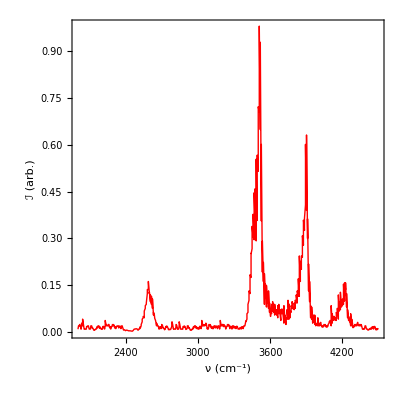
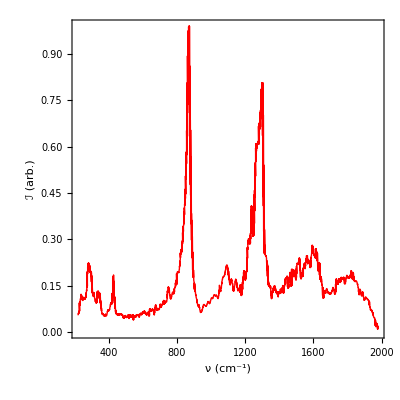
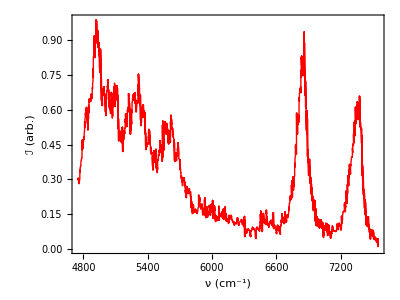
```mathematica
sampSpec=-Graphics-;
sampSpec2=-Graphics-;
sampSpec3=-Graphics-;
```

```mathematica
FirstCase[sampSpec3, Line[data_]:>data, None, ∞]
```

```mathematica
pointData=
FirstCase[#, Line[data_]:>data, None, ∞]&/@{sampSpec, sampSpec2, sampSpec3};
```

```mathematica
plotShow[spec_, freqs_]:=
Show[
spec,
FrameStyle->Black,
AspectRatio->.5,
Epilog->
{
Blue,
Arrowheads[Small],
Map[Arrow[{{#, 1}, {#, .95}}]&, freqs]
},
BaseStyle->
{
FontColor->Black,
FontFamily->"CMU Serif",
FontSize->20
},
FrameTicks->{{None, None}, {Automatic, None}}
]
```

#### Old Sad Stuff

```mathematica
scaledShiftedFreqs=
Join[
379+.75(#-#[[1]])&@allPoints["Frequencies"][[1;;10;;2]],
3520+.75(#-#[[1]])&@trueShifts
];
```

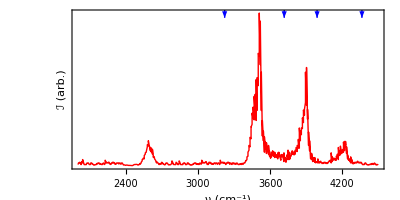

```mathematica
plotShow[sampFreq,trueShifts]
```

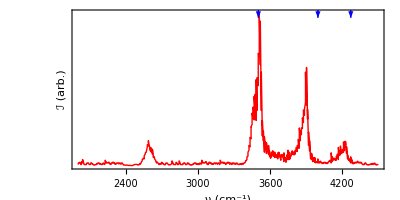

```mathematica
shift1=plotShow[sampFreq,280+trueShifts]
```

```mathematica
expFig["shiftedResults", Pane[Show[shift1, AspectRatio->1], 500]]
```

/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/shiftedResults.pdf

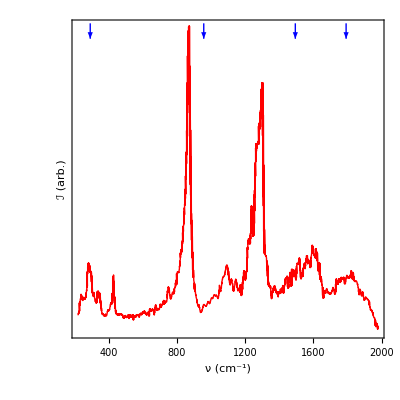

```mathematica
shift2=Pane[Show[plotShow[sampSpec1, allPoints["Frequencies"][[1;;25;;2]]-150], AspectRatio->1], 500]
```

```mathematica
expFig["shiftedResults_low", shift2]
```

/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/shiftedResults_low.pdf

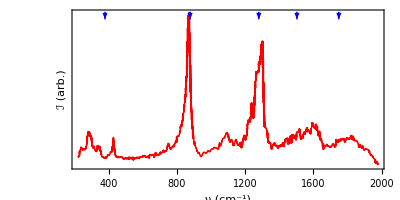

```mathematica
plotShow[sampSpec1, scaledShiftedFreqs]
```

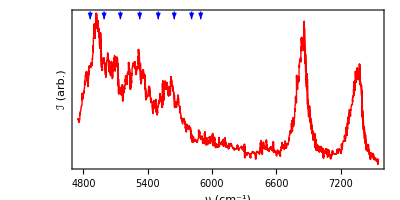

```mathematica
plotShow[sampSpec3, trueShifts]
```

#### Newer Still Sad Stuff

```mathematica
<<ChemTools`Spectroscopy`
```

```mathematica
sadSpec=ChemSpectrum[…];
```

```mathematica
sadSpec@"Plot"[ImageSize->500, ImageSize->700, AspectRatio->.5, PlotRange->{{0, 7500}, {0, All}},
Frame->True, FrameStyle->Black,
FrameTicks->
{
{
{#, StringReplace[ToString[#], {StartOfString~~".":>"0.", "."~~EndOfString->".0"}], {.01, 0}, {}}&/@
Range[.05, 1, .1],
None
}, 
{
{#, ToString[#], {.01, 0}, {}}&/@Range[500, 6000, 1000],
None
}
}
]
```

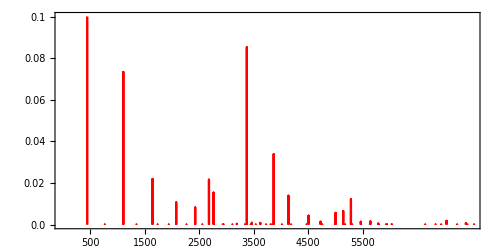

```mathematica
sadSpec@"Plot"[
ImageSize->500, ImageSize->700, AspectRatio->.5, PlotRange->{{0, 7500}, {0, .1}},
Frame->True, FrameStyle->Black,
FrameTicks->
{
{
{#, StringReplace[ToString[#], {StartOfString~~".":>"0.", "."~~EndOfString->".0"}], {.01, 0}, {}}&/@
Range[0, .1, .01],
None
}, 
{
{#, ToString[#], {.01, 0}, {}}&/@Range[500, 6000, 1000],
None
}
}
]
```

```mathematica
shiftScaleSpec=sadSpec["Shift"[150]]["Scale"[1.25,  3520]];
```

```mathematica
hmmSpec=
With[{spec=shiftScaleSpec@"Window"[{4750, 7350}]},
spec@"Plot"[ImageSize->500, ImageSize->700, AspectRatio->.5, 
PlotRange->{{4750, 7350}, {0, All}},
Frame->True, FrameStyle->Black
]
];
```

#### Real Comparisons

```mathematica
sadSpecOld=ChemSpectrum[…];
```

```mathematica
sadSpec2=ChemSpectrum[…];
```

```mathematica
sadSpec=ChemSpectrum[…];
specNoCouple=
{ChemSpectrum[…],ChemSpectrum[…],ChemSpectrum[…],ChemSpectrum[…],ChemSpectrum[…],ChemSpectrum[…]};
```

```mathematica
digitData=;
```

```mathematica
spectra=
ChemSpectrum/@
MapThread[
Transpose[{1, #3}*Transpose[MovingAverage[#, #2]]]&,
{
digitData[[{2, 1, 3}]],
{125, 50, 100},
{.08, .1, .01}
}
];
joinedSpec=ChemSpectrum[Join@@Map[#["Points"]&, spectra]];
```

```mathematica
zhouSpec=ChemSpectrum[…];
```

```mathematica
spectrumPlot//Clear
spectrumPlot[spec_, max:_?NumericQ|All:All, ops:OptionsPattern[]]:=
spec@"Plot"[
Sequence@@
FilterRules[{ops},
Except[FrameTicks]
],
PlotRange->{All, {0, max}},
Frame->True,
FrameLabel->{"ω (cm^-1)", "ℐ (arb.)"},
LabelStyle->{FontSize->18, FontFamily->"CMU Serif"},
AspectRatio->.5,
ImageSize->500,
FrameTicksStyle->Directive[Black, Thick],
FrameTicks->
(
ReplaceAll[#, {p_, l_, {_, _}, d_}:>{p, l, {.01, 0}, d}]&@
{
{
Lookup[
{ops},
FrameTicks,
{
None
}
][[1]],
None
},
{
Replace[
Lookup[
{ops},
FrameTicks,
{
None,
Automatic
}
][[2]],
Automatic:>
Charting`ScaledTicks[
{Identity, Identity}
][Apply[Sequence, Round[(Mean[#]+.9(#-Mean[#])), 50]&[spec["FrequencyRange"]]], 5]
],
None
}
}
)
]
```

```mathematica
zapDapTap=
MapIndexed[
Show[
spectrumPlot[#, 
PlotStyle->Directive[ColorData[97][3], Opacity[.5]],
Filling->Axis,
FillingStyle->Opacity[.5],
AspectRatio->.33,
PlotRange->{All, {-.0150/(10^(#2[[1]]*2/3)), All}}
],
spectrumPlot[zhouSpec, PlotStyle->Blue],
spectrumPlot[sadSpec],
Switch[#2[[1]],
3,
FrameLabel->{"ω (cm^-1)", ""},
2,
FrameLabel->{None, "ℐ (arb.)"},
_,
FrameLabel->{None, ""}
],
FrameStyle->Black
]&,
spectra
];
```

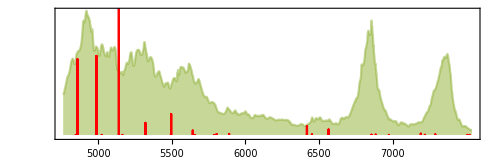

```mathematica
zapDapTap[[-1]]
```

```mathematica
makeStateLabel//Clear
makeStateLabel[i_Integer, lab_]:=
If[i==0, Nothing, Subsuperscript["ν", i, lab]];
makeStateLabel[i_Integer]:=
makeStateLabel[i, Superscript[Style["H", Plain], "+"]];
makeStateLabel["No Clue"]:="ν_(?? ?)";
makeStateLabel[{i_, Positive}]:=
Row@{Ceiling@i,Subscript["ν", Subscript[Style["Rxn", Plain], "+"]]};
makeStateLabel[{i_, Negative}]:=
Row@{Ceiling@i,Subscript["ν", Subscript[Style["Rxn", Plain], "-"]]};
makeStateLabel[{i_, s_String}]:=makeStateLabel[i];
makeStateLabel[{n_, Plus, m_}]:=Row@{makeStateLabel[n], "+", makeStateLabel[m]};
makeStateLabel[{n_, Subtract, m_}]:=Row@{makeStateLabel[n], "-", makeStateLabel[m]};
```

```mathematica
labels=
Join[
makeStateLabel/@gsPlotSels,
MapThread[
Row[
{
Row@{
"(",
Row[{Subscript["ν", "A"], makeStateLabel[#]}, "+"],
")"
}, 
Row@{
"(",
Row[{Subscript["ν", "S"], makeStateLabel[#2]}, "+"],
")"
}
},
"+"
]&,
betterStateDivisions[[All, statesToPlot[[All, 1]]]]
],
MapThread[
Row[
{
Row@{"(",Row[{ Row@{2, Subscript["ν", "A"]},  makeStateLabel[#]}, "+"], ")"},
Row@{"(", 
Row[{Subscript["ν", "A"], Subscript["ν", "S"],makeStateLabel[#2]}, "+"], ")"},
Row@{"(", 
Row[{
Row@{2,  Subscript["ν", "S"]}, makeStateLabel[#3]
},
"+"
], ")"}
},
"+"
]&,
baseStates456
]
];
```

```mathematica
peakPositions=
SortBy[First]@Join[
MaximalBy[sadSpec[[;;25]]@"Points", Last, Length@gsPlotSels],
MaximalBy[sadSpec[[26;;50]]@"Points", Last, Length@statesToPlot],
MaximalBy[sadSpec[[51;;]]@"Points", Last, Length@baseStates456]
];
```

```mathematica
clumps=
Thread@
{
TakeList[labels, {3,7, 8}],
TakeList[{#[[1]], If[#[[2]]>.1, .08, #[[2]]]}&/@peakPositions, {3,7, 8}]
};
```

```mathematica
labeleldSpeccasdasd=
MapIndexed[
Show[
spectrumPlot[#, 
PlotStyle->Directive[ColorData[97][3], Opacity[.5]],
Filling->Axis,
FillingStyle->Opacity[.5],
AspectRatio->.33,
PlotRange->{All, {-.0150/(10^(#2[[1]]*2/3)), All}}
],
spectrumPlot[zhouSpec, PlotStyle->Blue],
spectrumPlot[sadSpec,PlotStyle->Red],
Switch[#2[[1]],
3,
FrameLabel->{"ω (cm^-1)", ""},
2,
FrameLabel->{None, "ℐ (arb.)"},
_,
FrameLabel->{None, ""}
],
FrameStyle->Black,
Epilog->
MapThread[Text[#, #2, {0, 0}]&, clumps[[#2[[1]]]]]
]&,
spectra
]
```

```mathematica
MapIndexed[
Export[
presFigFile["labels/vibration_"<>ToString@#2[[1]]],
figStyleText@#
]&,
labels
];
```

```mathematica
expFig[
presFigFile["labels_column"],
Grid[
labeleldSpeccasdasd//List//Transpose,
Spacings->{0, -.1}
]
]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/labels_column.pdf

```mathematica
expFig[
presFigFile["spec_column"],
Grid[
zapDapTap//List//Transpose,
Spacings->{0, -.1}
]
]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/spec_column.pdf

```mathematica
MapIndexed[
expFig[
presFigFile["spec_chunk_"<>ToString@#2[[1]]],
Show[
spectrumPlot[#, 
PlotStyle->Directive[ColorData[97][3], Opacity[.5]],
Filling->Axis,
FillingStyle->Opacity[.5],
AspectRatio->.33
],
spectrumPlot[zhouSpec, PlotStyle->Blue],
spectrumPlot[sadSpec]
]
]&,
spectra
]
```

{$Failed,$Failed,$Failed}

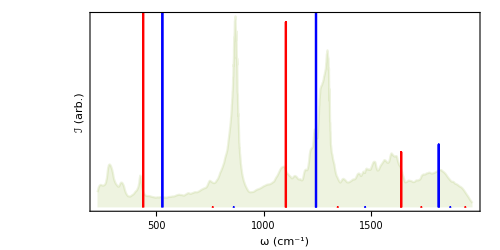

```mathematica
specChunk1=
Show[
spectrumPlot[spectra[[1]], 
PlotStyle->Directive[ColorData[97][3], Opacity[.15]],
Filling->Axis,
FillingStyle->Opacity[.15]
],
spectrumPlot[zhouSpec, PlotStyle->Blue],
spectrumPlot[sadSpec]
]
```

```mathematica
expFig["spec_chunk_1", specChunk1]
```

/Users/Mark/Documents/UW/Research/Second Year/Research Summary/figures/spec_chunk_1.pdf

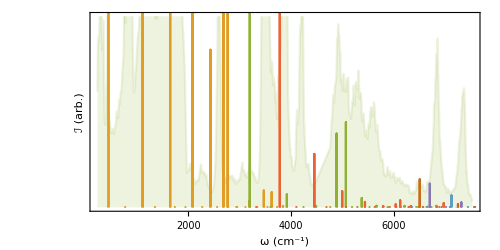

```mathematica
Show[
spectrumPlot[joinedSpec, .01,
PlotStyle->Directive[ColorData[97][3], Opacity[.15]],
Filling->Axis,
FillingStyle->Opacity[.15]
],
MapIndexed[#@"Plot"[PlotStyle->ColorData[97][1+#2[[1]]]]&, specNoCouple]
]
```

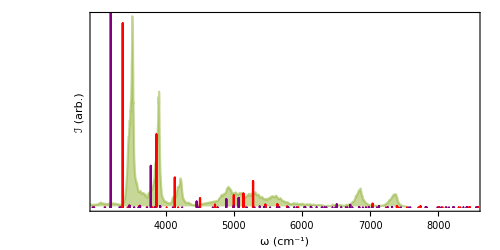

```mathematica
noCouplePlot=
Show[
spectrumPlot[joinedSpec, 
PlotRange->{{3000, 8500},{0.0001, All}},
PlotStyle->Directive[ColorData[97][3], Opacity[.5]],
Filling->Axis,
FillingStyle->Opacity[.5],
FrameTicks->{None,
Charting`ScaledTicks[
{Identity, Identity}
][Apply[Sequence, Round[(Mean[#]+.9(#-Mean[#])), 50]&[{3000, 8500}]], 5]
}
],
sadSpec@"Plot"[],
MapIndexed[
#@"Plot"[PlotStyle->Purple]&,
 specNoCouple
]
]
```

```mathematica
expFig[presFigFile@"no_coupling", noCouplePlot]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/no_coupling.pdf

```mathematica
expFig["no_coupling", noCouplePlot]
```

/Users/Mark/Documents/UW/Research/Second Year/Research Summary/figures/no_coupling.pdf

```mathematica
joinedSpec@"Scale"[{1, 0}, {.1, 0} ]
```

```mathematica
expFig[
"broken_scale",
Show[
spectrumPlot[
joinedSpec, 
PlotRange->{{6500, 8500},{0, .01}},
PlotStyle->Directive[ColorData[97][3], Opacity[.5]],
Filling->Axis,
FillingStyle->Opacity[.5],
FrameTicks->{None,
Charting`ScaledTicks[
{Identity, Identity}
][Apply[Sequence, Round[(Mean[#]+.9(#-Mean[#])), 50]&[{3000, 8000}]], 5]
}
],
sadSpec["Scale"[{1, 0}, {5, 0} ]]@"Plot"[](*,
(*MapIndexed[
#@"Plot"[PlotStyle->Blue]&,
 specNoCouple
]*)*)
]
]
```

$Failed

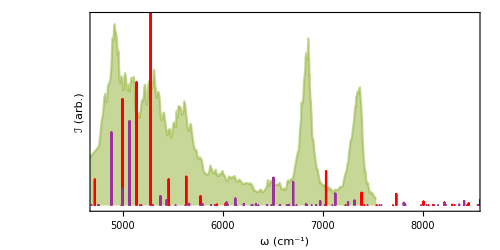

```mathematica
noCouplePlot2=
Show[
spectrumPlot[joinedSpec, 
PlotRange->{{4750, 8500},{-0.0001, .01}},
PlotStyle->Directive[ColorData[97][3], Opacity[.5]],
Filling->Axis,
FillingStyle->Opacity[.5],
FrameTicks->{None,
Charting`ScaledTicks[
{Identity, Identity}
][Apply[Sequence, Round[(Mean[#]+.9(#-Mean[#])), 50]&[{3000, 8500}]], 5]
}
],
sadSpec@"Plot"[],
MapIndexed[
#@"Plot"[PlotStyle->Lighter[Purple, .2]]&,
 specNoCouple
]
]
```

```mathematica
expFig[presFigFile@"no_coupling_higher", noCouplePlot2]
```

/Users/Mark/Documents/UW/Research/Second Year/Presentation/figures/no_coupling_higher.pdf

```mathematica
expFig["no_coupling_higher", noCouplePlot2]
```

$Failed

```mathematica
expFig["no_coupling", noCouplePlot]
```

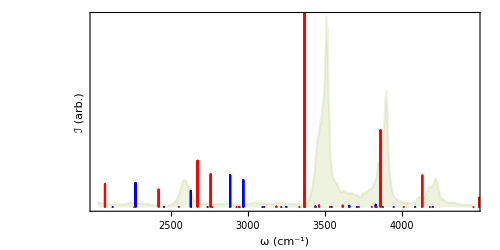

```mathematica
spec2=
Show[
spectrumPlot[spectra[[2]], 
PlotStyle->Directive[ColorData[97][3], Opacity[.15]],
Filling->Axis,
FillingStyle->Opacity[.15]
],
spectrumPlot[zhouSpec, PlotStyle->Blue],
spectrumPlot[sadSpec]
]
```

```mathematica
expFig["spec_chunk_2", spec2]
```

/Users/Mark/Documents/UW/Research/Second Year/Research Summary/figures/spec_chunk_2.pdf

```mathematica
dist=PDF[sadSpec@"NormalDistribution"[45], ω];
zhouDist=PDF[zhouSpec@"NormalDistribution"[45], ω];
```

```mathematica
Show[
spectrumPlot[joinedSpec,
PlotStyle->ColorData[97][3],
Filling->Axis,
FillingStyle->Opacity[.15]
],
Plot[-Evaluate[150*dist], {ω, 200, 7500}, PlotRange->All, 
PlotStyle->Blend[{ColorData[97][4], Red}],
Filling->Axis,
FillingStyle->Opacity[.15]
],
PlotRange->{{200, 7500}, {-.1, .1}} 
]//Quiet
```

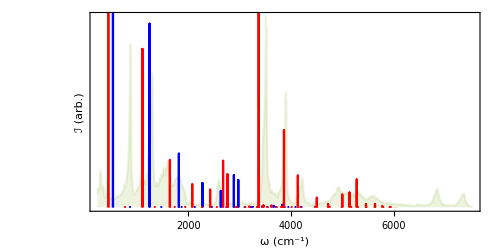

```mathematica
zhouCompSpec=
Show[
spectrumPlot[joinedSpec,
PlotStyle->Directive[ColorData[97][3], Opacity[.15]],
Filling->Axis,
FillingStyle->Opacity[.15]
],
spectrumPlot[zhouSpec, PlotStyle->Blue],
spectrumPlot[sadSpec]
]
```

```mathematica
expFig["zhou_comp", zhouCompSpec]
```

/Users/Mark/Documents/UW/Research/Second Year/Research Summary/figures/zhou_comp.pdf

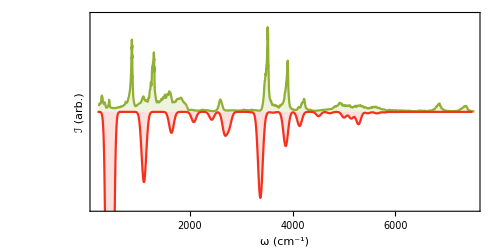

```mathematica
compSpec=
Show[
spectrumPlot[joinedSpec,
PlotStyle->ColorData[97][3],
Filling->Axis,
FillingStyle->Opacity[.15]
],
Plot[-Evaluate[150*dist], {ω, 200, 7500}, PlotRange->All, 
PlotStyle->Blend[{ColorData[97][4], Red}],
Filling->Axis,
FillingStyle->Opacity[.15]
],
PlotRange->{{200, 7500}, {-.1, .1}} 
]//Quiet
```

```mathematica
expFig["comp_spec", compSpec]
```

/Users/Mark/Documents/UW/Research/Second Year/Research Summary/figures/comp_spec.pdf

#### Old Overlay

```mathematica
meep=
Show[
hmmSpec,
Prolog->
Inset[asd, Scaled[{1, .001}], {Right, Bottom}, 1.05*-Map[Apply[Subtract], PlotRange@hmmSpec]],
ImageSize->ImageDimensions[asd]/2, (*FrameTicks->None,*) 
AspectRatio->Apply[Divide, Reverse@ImageDimensions[asd]],
BaseStyle->{FontSize->20}
]
```

```mathematica
Export[figureFile["prelimResult"], meep, Background->None]
```

/Users/Mark/Documents/UW/Research/Presentation/TGM 1:14:19/out/prelimResult.png

```mathematica
(*,
FrameTicks->
{
{
{#, ScientificForm[N@#], {.01, 0}, {}}&/@Range[0.5*10^-7, 8*10^-7, 2.5*10^-7],
None
}, 
{
{#, Rotate[ToString[#], -π/2], {.01, 0}, {}}&/@Range[5000, 7000, 500],
None
}
}*)
(*,
Epilog->
Map[
{
{
Gray,
Line[{#+{20, .1*10^-8}, #+{50, 1.5*10^-8}, #+{80, 1.5*10^-8}}]
},
Text[
Framed[ToString@#[[1]], 
Background->GrayLevel[1, .6], FrameStyle->GrayLevel[.3, .5], 
FrameMargins->{{5, 5}, {0, 0}}], #+{100, 0}, {-1, -.2}]
}&,
spec["Window"[{0, ∞}, {5*10^-8, 1}]]["Points"]
]*)
```

### Coupling

```mathematica
betterThermo=
With[
{
scheme=
KeyValueMap[
Blend[{#2, White}, 
If[#<0, 0, #]&@Rescale[Abs[#-.5], {0, .125}, {1, 0}]
]&,
AssociationMap[
ColorData["ThermometerColors"],
Range[0, 1, .01]
]
]
},
Blend[scheme, #]&
];
```

```mathematica
smatGraphic=;
hmatUGraphic=;
hmatGraphic=;
```

```mathematica
expFig["coupling_example", couplingGridGraphic]
```

/Users/Mark/Documents/UW/Research/Second Year/Research Summary/figures/coupling_example.pdf

```mathematica
couplingGridGraphic=
Grid[{
{"H No Coupling", "S", "H Coupling"},
Show[#, Frame->False, ImageSize->150]&/@{hmatUGraphic, smatGraphic, hmatGraphic}
},
BaseStyle->{FontFamily->"CMU Serif"}
];
```